```mathematica
MinGen[X_] := If[FreeQ[X,Around],Min[X],Min[#["Value"]& /@ X]];
MaxGen[X_] := If[FreeQ[X,Around],Max[X],Max[#["Value"]& /@ X]]
```

```mathematica
MinVal[L_, n_]:= MinGen[Transpose[L][[n]]];
```

```mathematica
MaxVal[L_, n_]:= MaxGen[Transpose[L][[n]]];
```

```mathematica
MinGen[{Around[1,0.1],Around[3,0.2]}]
```

1.

```mathematica
MinGen[{1,0.1,3,0.2}]
```

0.1

```mathematica
MyDnSample[L_, n_] := L[[#]]& /@Range[1,Length[L],n];
```

```mathematica
DataWithErrors[data_,n_, bins_]:=Around[#[[1]],#[[2]]] &/@ Transpose[{Mean[#],StandardDeviation[#]/Sqrt[bins]}]& /@ Partition[Sort[data,#1[[n]]<#2[[n]]&],bins];
```

```mathematica
DataWithErrors[data_, bins_]:=Around[#[[1]],#[[2]]] &/@ Transpose[{Mean[#],StandardDeviation[#]/Sqrt[bins]}]& /@ Partition[data,bins];
```

```mathematica
DataWithWeights[data_, bins_]:={Mean[#],Sqrt[bins]/StandardDeviation[#]}& /@ Partition[data,bins];
```

```mathematica
{dd,ww} =Transpose[DataWithWeights[Table[N[{x, Sin[Pi x]}],{x,-1,1,1/1000}],100]]
```

{{{-0.9505,-0.154247},{-0.8505,-0.450732},{-0.7505,-0.703096},{-0.6505,-0.886636},{-0.5505,-0.983386},{-0.4505,-0.983876},{-0.3505,-0.888056},{-0.2505,-0.705308},{-0.1505,-0.453519},{-0.0505,-0.157337},{0.0495,0.154247},{0.1495,0.450732},{0.2495,0.703096},{0.3495,0.886636},{0.4495,0.983386},{0.5495,0.983876},{0.6495,0.888056},{0.7495,0.705308},{0.8495,0.453519},{0.9495,0.157337}},{{344.691,111.331},{344.691,123.319},{344.691,155.178},{344.691,240.772},{344.691,674.834},{344.691,687.491},{344.691,242.249},{344.691,155.665},{344.691,123.517},{344.691,111.386},{344.691,111.331},{344.691,123.319},{344.691,155.178},{344.691,240.772},{344.691,674.834},{344.691,687.491},{344.691,242.249},{344.691,155.665},{344.691,123.517},{344.691,111.386}}}

```mathematica
dd[[;;5]]
```

{{-0.9505,-0.154247},{-0.8505,-0.450732},{-0.7505,-0.703096},{-0.6505,-0.886636},{-0.5505,-0.983386}}

```mathematica
ww[[;;5]]
```

{{344.691,111.331},{344.691,123.319},{344.691,155.178},{344.691,240.772},{344.691,674.834}}

```mathematica
Around[#[[1]],#[[2]]]& /@Transpose[{{m,m,m},{s,s,s}}]
```

{ms,ms,ms}

```mathematica
ttt=Transpose[{Table[RandomReal[],4],Table[RandomReal[],4],Table[RandomReal[],4]}]
```

{{0.162724,0.825891,0.934598},{0.199885,0.145958,0.458536},{0.0697615,0.802551,0.0866016},{0.265618,0.424608,0.790749}}

```mathematica
Mean[#]& /@Partition[ttt,2]
```

{{0.181305,0.485925,0.696567},{0.16769,0.61358,0.438675}}

```mathematica
ttt[[;;3]]
```

{{0.162724,0.825891,0.934598},{0.199885,0.145958,0.458536},{0.0697615,0.802551,0.0866016}}

```mathematica
Transpose[{{1,2},{a,b}, {x,y}}]
```

{{1,a,x},{2,b,y}}

```mathematica
test = Transpose[{ttt}];
```

```mathematica
Dimensions[ttt]
```

{4,3}

```mathematica
test =DataWithErrors[ArrayReshape[Sort[Table[RandomReal[],256]],{64,4}],4]
```

{{0.0350.015,0.0420.014,0.0460.012,0.0530.011},{0.1150.014,0.1170.014,0.1200.013,0.1260.012},{0.1780.009,0.1800.007,0.1850.006,0.1890.005},{0.2370.012,0.2400.012,0.2420.012,0.2480.009},{0.2920.008,0.2950.007,0.2990.007,0.3030.007},{0.3540.010,0.3590.009,0.3610.008,0.3630.008},{0.4020.010,0.4060.010,0.4100.010,0.4120.010},{0.4660.014,0.4720.016,0.4800.014,0.4820.015},{0.5510.013,0.5560.012,0.5590.010,0.5660.008},{0.6010.006,0.6020.006,0.6060.005,0.6070.006},{0.6590.012,0.6620.013,0.6710.012,0.6750.014},{0.7260.007,0.7300.009,0.7330.010,0.7370.008},{0.7860.008,0.7880.007,0.7900.006,0.7940.006},{0.8290.007,0.8340.007,0.8360.006,0.8390.007},{0.8870.010,0.8880.010,0.8930.008,0.8970.008},{0.9460.013,0.9480.013,0.9560.013,0.9610.013}}

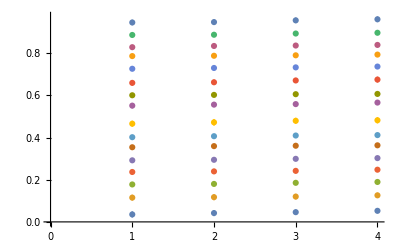

```mathematica
ListPlot[test]
```

```mathematica
ShowFitModel[data_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
Show[
ListPlot[data, PlotStyle->{dcol},PlotLegends->{"data"}],
Plot[model[x],{x,MinVal[data,1],MaxVal[data,1]},PlotStyle->{mcol, Thick},
PlotLegends->{N[model[Xlabel],7]},PlotRange->All],
PlotLabel->title,
AxesLabel->{Xlabel, Ylabel}
];
ShowLogFitModel[data_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
Show[
ListPlot[data, PlotStyle->{dcol},PlotLegends->{Ylabel}],
Plot[model[x],{x,MinVal[data,1],MaxVal[data,1]},PlotStyle->{mcol, PointSize[0.5]},
PlotLegends->{N[FullSimplify[Exp[model[Log[x]]]],7]},PlotRange->All],
PlotLabel->title,
AxesLabel->{Xlabel, Ylabel}
];
```

```mathematica
ShowLogFitModelBin[data_,bins_, model_,Xlabel_,Ylabel_, title_, dcol_, mcol_]:=
ShowLogFitModel[DataWithErrors[data,1,bins], model,Xlabel,Ylabel, title, dcol, mcol];
```

```mathematica
ClearAll[NumericalVector];
```

```mathematica
NumericalVector[{}] = False;
```

```mathematica
NumericVector[X_] := And @@(NumericQ  /@ X);
```

```mathematica
NumericVector[{1,2,3}]
```

True

```mathematica
edectab={{-4.605170185988091,8.411754927159429},{-4.586749505244138,8.411754884354794},{-4.5683288245001865,8.411754840755801},{-4.549908143756234,8.411754796347722},{-4.531487463012282,8.411754751115557},{-4.5130667822683295,8.411754705044029},{-4.494646101524377,8.411754658117571},{-4.476225420780424,8.411754610320342},{-4.457804740036472,8.411754561636192},{-4.43938405929252,8.411754512048685},{-4.420963378548567,8.411754461541072},{-4.402542697804615,8.4117544100963},{-4.384122017060663,8.411754357696994},{-4.36570133631671,8.411754304325465},{-4.347280655572758,8.411754249963689},{-4.328859974828806,8.411754194593316},{-4.310439294084854,8.411754138195649},{-4.292018613340901,8.411754080751649},{-4.273597932596949,8.411754022241928},{-4.255177251852996,8.41175396264673},{-4.236756571109044,8.411753901945943},{-4.218335890365092,8.411753840119076},{-4.199915209621139,8.411753777145265},{-4.181494528877187,8.411753713003254},{-4.1630738481332346,8.411753647671397},{-4.144653167389282,8.411753581127648},{-4.12623248664533,8.41175351334955},{-4.1078118059013775,8.411753444314238},{-4.089391125157425,8.411753373998414},{-4.070970444413473,8.411753302378356},{-4.0525497636695205,8.411753229429902},{-4.034129082925568,8.41175315512844},{-4.015708402181615,8.411753079448909},{-3.9972877214376634,8.411753002365778},{-3.9788670406937108,8.411752923853049},{-3.9604463599497586,8.411752843884242},{-3.9420256792058064,8.411752762432384},{-3.9236049984618537,8.411752679470007},{-3.9051843177179015,8.411752594969133},{-3.886763636973949,8.41175250890127},{-3.8683429562299967,8.411752421237393},{-3.8499222754860445,8.41175233194795},{-3.831501594742092,8.411752241002835},{-3.8130809139981396,8.41175214837139},{-3.794660233254187,8.411752054022385},{-3.776239552510235,8.41175195792402},{-3.7578188717662826,8.411751860043902},{-3.73939819102233,8.411751760349043},{-3.7209775102783778,8.411751658805843},{-3.702556829534425,8.41175155538008},{-3.684136148790473,8.411751450036906},{-3.6657154680465203,8.411751342740823},{-3.6472947873025685,8.411751233455679},{-3.628874106558616,8.411751122144654},{-3.6104534258146637,8.41175100877025},{-3.592032745070711,8.411750893294274},{-3.573612064326759,8.41175077567783},{-3.555191383582806,8.411750655881299},{-3.536770702838854,8.411750533864337},{-3.5183500220949018,8.411750409585851},{-3.4999293413509496,8.41175028300399},{-3.481508660606997,8.411750154076131},{-3.4630879798630447,8.411750022758861},{-3.444667299119092,8.411749889007972},{-3.42624661837514,8.411749752778434},{-3.4078259376311877,8.411749614024387},{-3.389405256887235,8.41174947269913},{-3.370984576143283,8.41174932875509},{-3.35256389539933,8.411749182143826},{-3.334143214655378,8.411749032815997},{-3.3157225339114254,8.411748880721355},{-3.297301853167473,8.411748725808723},{-3.278881172423521,8.411748568025981},{-3.2604604916795688,8.411748407320047},{-3.242039810935616,8.41174824363686},{-3.223619130191664,8.411748076921361},{-3.2051984494477113,8.411747907117483},{-3.186777768703759,8.41174773416812},{-3.1683570879598064,8.41174755801511},{-3.149936407215854,8.41174737859922},{-3.1315157264719016,8.411747195860123},{-3.11309504572795,8.411747009736384},{-3.094674364983997,8.411746820165433},{-3.076253684240045,8.411746627083549},{-3.0578330034960928,8.411746430425827},{-3.03941232275214,8.411746230126182},{-3.020991642008188,8.411746026117296},{-3.0025709612642357,8.411745818330619},{-2.9841502805202835,8.411745606696334},{-2.965729599776331,8.411745391143343},{-2.9473089190323782,8.41174517159923},{-2.928888238288426,8.411744947990254},{-2.9104675575444734,8.411744720241309},{-2.892046876800521,8.411744488275907},{-2.873626196056569,8.411744252016153},{-2.855205515312617,8.411744011382718},{-2.836784834568664,8.411743766294808},{-2.8183641538247115,8.411743516670148},{-2.7999434730807593,8.411743262424945},{-2.781522792336807,8.411743003473863},{-2.763102111592855,8.411742739729997},{-2.744681430848902,8.41174247110484},{-2.7262607501049496,8.41174219750826},{-2.707840069360998,8.411741918848463},{-2.6894193886170457,8.411741635031968},{-2.670998707873093,8.411741345963572},{-2.652578027129141,8.411741051546322},{-2.634157346385188,8.41174075168148},{-2.615736665641236,8.411740446268498},{-2.5973159848972833,8.411740135204969},{-2.578895304153331,8.411739818386613},{-2.5604746234093785,8.411739495707224},{-2.5420539426654263,8.41173916705865},{-2.523633261921474,8.411738832330746},{-2.5052125811775214,8.411738491411347},{-2.4867919004335692,8.411738144186222},{-2.468371219689617,8.411737790539043},{-2.4499505389456644,8.411737430351346},{-2.431529858201712,8.411737063502486},{-2.41310917745776,8.411736689869606},{-2.3946884967138073,8.41173630932759},{-2.376267815969855,8.411735921749024},{-2.357847135225903,8.411735527004154},{-2.3394264544819503,8.411735124960844},{-2.3210057737379977,8.411734715484531},{-2.3025850929940455,8.411734298438184},{-2.2841644122500933,8.411733873682252},{-2.265743731506141,8.411733441074626},{-2.2473230507621884,8.41173300047059},{-2.2289023700182358,8.411732551722773},{-2.2104816892742836,8.411732094681097},{-2.1920610085303314,8.411731629192733},{-2.1736403277863787,8.411731155102046},{-2.1552196470424265,8.411730672250549},{-2.136798966298474,8.411730180476848},{-2.1183782855545217,8.411729679616586},{-2.0999576048105695,8.411729169502399},{-2.081536924066617,8.411728649963848},{-2.0631162433226646,8.411728120827375},{-2.044695562578712,8.411727581916242},{-2.02627488183476,8.411727033050475},{-2.007854201090808,8.4117264740468},{-1.9894335203468554,8.411725904718578},{-1.9710128396029032,8.41172532487576},{-1.952592158858951,8.411724734324814},{-1.9341714781149986,8.41172413286866},{-1.915750797371046,8.411723520306614},{-1.8973301166270937,8.411722896434316},{-1.878909435883141,8.411722261043666},{-1.8604887551391889,8.411721613922756},{-1.8420680743952367,8.411720954855799},{-1.8236473936512843,8.411720283623062},{-1.8052267129073318,8.411719600000787},{-1.7868060321633792,8.411718903761132},{-1.768385351419427,8.41171819467208},{-1.7499646706754746,8.411717472497372},{-1.7315439899315221,8.411716736996427},{-1.71312330918757,8.411715987924275},{-1.6947026284436177,8.411715225031463},{-1.676281947699665,8.411714448063982},{-1.6578612669557125,8.411713656763185},{-1.6394405862117605,8.411712850865696},{-1.621019905467808,8.411712030103335},{-1.6025992247238559,8.411711194203017},{-1.5841785439799032,8.411710342886675},{-1.565757863235951,8.411709475871163},{-1.5473371824919986,8.411708592868168},{-1.528916501748046,8.411707693584114},{-1.5104958210040937,8.41170677772007},{-1.4920751402601413,8.411705844971651},{-1.473654459516189,8.41170489502892},{-1.4552337787722363,8.411703927576285},{-1.4368130980282847,8.411702942292406},{-1.4183924172843323,8.411701938850072},{-1.3999717365403799,8.411700916916114},{-1.3815510557964277,8.411699876151296},{-1.363130375052475,8.411698816210194},{-1.3447096943085228,8.4116977367411},{-1.3262890135645706,8.411696637385894},{-1.3078683328206184,8.41169551777994},{-1.2894476520766658,8.411694377551958},{-1.2710269713327134,8.411693216323915},{-1.2526062905887607,8.41169203371089},{-1.234185609844808,8.411690829320964},{-1.215764929100856,8.411689602755077},{-1.1973442483569035,8.411688353606923},{-1.1789235676129515,8.411687081462807},{-1.1605028868689988,8.411685785901508},{-1.1420822061250466,8.411684466494155},{-1.1236615253810942,8.411683122804076},{-1.1052408446371418,8.411681754386674},{-1.0868201638931894,8.411680360789271},{-1.0683994831492372,8.411678941550964},{-1.0499788024052845,8.411677496202483},{-1.031558121661332,8.41167602426604},{-1.0131374409173801,8.411674525255176},{-0.9947167601734275,8.411672998674602},{-0.976296079429475,8.411671444020044},{-0.957875398685523,8.411669860778085},{-0.9394547179415704,8.411668248425991},{-0.921034037197618,8.41166660643155},{-0.9026133564536655,8.411664934252904},{-0.884192675709713,8.411663231338382},{-0.8657719949657606,8.41166149712632},{-0.847351314221809,8.411659731044876},{-0.8289306334778566,8.411657932511861},{-0.8105099527339044,8.411656100934543},{-0.7920892719899515,8.411654235709465},{-0.7736685912459994,8.411652336222245},{-0.7552479105020471,8.411650401847396},{-0.7368272297580948,8.411648431948114},{-0.7184065490141424,8.411646425876084},{-0.6999858682701899,8.41164438297127},{-0.6815651875262373,8.411642302561704},{-0.663144506782285,8.411640183963273},{-0.6447238260383327,8.411638026479507},{-0.6263031452943802,8.411635829401371},{-0.6078824645504279,8.411633592007036},{-0.5894617838064755,8.411631313561637},{-0.5710411030625233,8.41162899331706},{-0.552620422318571,8.411626630511694},{-0.5341997415746187,8.411624224370197},{-0.515779060830666,8.41162177410325},{-0.4973583800867137,8.41161927890731},{-0.4789376993427614,8.411616737964358},{-0.46051701859880895,8.41161415044166},{-0.4420963378548566,8.411611515491478},{-0.42367565711090416,8.41160883225081},{-0.40525497636695185,8.41160609984112},{-0.3868342956229997,8.411603317368076},{-0.3684136148790471,8.411600483921267},{-0.3499929341350948,8.411597598573904},{-0.3315722533911424,8.41159466038254},{-0.31315157264718985,8.411591668386784},{-0.2947308919032375,8.411588621608987},{-0.2763102111592856,8.411585519053952},{-0.2578895304153332,8.411582359708614},{-0.23946884967138102,8.411579142541733},{-0.22104816892742854,8.411575866503565},{-0.2026274881834758,8.411572530525552},{-0.18420680743952383,8.411569133519977},{-0.16578612669557144,8.411565674379636},{-0.14736544595161913,8.411562151977487},{-0.12894476520766635,8.411558565166304},{-0.11052408446371438,8.411554912778334},{-0.09210340371976193,8.411551193624911},{-0.07368272297580956,8.411547406496108},{-0.05526204223185683,8.411543550160367},{-0.036841361487904546,8.411539623364126},{-0.018420680743952294,8.411535624831425},{0.,8.411531553263499},{0.018420680743952523,8.411527407338404},{0.036841361487905025,8.411523185710596},{0.0552620422318571,8.411518887010528},{0.07368272297580973,8.411514509844222},{0.0921034037197619,8.411510052792858},{0.11052408446371421,8.411505514412319},{0.12894476520766676,8.411500893232777},{0.14736544595161946,8.411496187758242},{0.16578612669557136,8.411491396466102},{0.18420680743952425,8.411486517806626},{0.2026274881834763,8.411481550202526},{0.22104816892742876,8.41147649204847},{0.239468849671381,8.41147134171061},{0.2578895304153335,8.411466097526073},{0.27631021115928556,8.411460757802459},{0.29473089190323815,8.41145532081733},{0.3131515726471905,8.411449784817696},{0.3315722533911431,8.411444148019475},{0.3499929341350951,8.411438408606957},{0.3684136148790477,8.411432564732275},{0.3868342956230004,8.411426614514834},{0.4052549763669526,8.411420556040751},{0.4236756571109051,8.411414387362285},{0.4420963378548575,8.41140810649725},{0.4605170185988096,8.41140171142842},{0.47893769934276204,8.411395200102929},{0.49735838008671474,8.411388570431662},{0.5157790608306667,8.411381820288607},{0.5341997415746192,8.41137494751023},{0.5526204223185716,8.411367949894874},{0.5710411030625239,8.411360825202092},{0.5894617838064753,8.411353571151976},{0.6078824645504276,8.411346185424474},{0.62630314529438,8.411338665658702},{0.6447238260383327,8.41133100945225},{0.663144506782285,8.411323214360475},{0.6815651875262373,8.41131527789579},{0.6999858682701895,8.411307197526916},{0.7184065490141421,8.411298970678134},{0.7368272297580942,8.411290594728536},{0.7552479105020468,8.411282067011298},{0.7736685912459994,8.411273384812903},{0.7920892719899516,8.411264545372292},{0.8105099527339038,8.411255545880048},{0.8289306334778563,8.411246383477602},{0.8473513142218085,8.411237055256407},{0.8657719949657611,8.411227558257094},{0.8841926757097135,8.411217889468606},{0.9026133564536658,8.411208045827335},{0.9210340371976181,8.411198024216235},{0.9394547179415706,8.411187821463916},{0.957875398685523,8.41117743434374},{0.9762960794294749,8.411166859572871},{0.9947167601734275,8.411156093811329},{1.0131374409173801,8.411145133661062},{1.0315581216613325,8.411133975664999},{1.049978802405285,8.411122616306033},{1.0683994831492372,8.411111052006005},{1.0868201638931896,8.411099279124684},{1.1052408446371418,8.411087293958747},{1.1236615253810944,8.411075092740715},{1.142082206125047,8.41106267163789},{1.160502886868999,8.411050026751257},{1.1789235676129517,8.411037154114423},{1.1973442483569037,8.41102404969248},{1.2157649291008563,8.411010709380832},{1.2341856098448087,8.410997129004077},{1.2526062905887612,8.410983304314817},{1.2710269713327134,8.410969230992487},{1.2894476520766658,8.410954904642137},{1.3078683328206184,8.410940320793216},{1.3262890135645706,8.410925474898317},{1.344709694308523,8.410910362331924},{1.363130375052475,8.410894978389125},{1.3815510557964277,8.410879318284303},{1.3999717365403799,8.41086337714982},{1.4183924172843323,8.410847150034678},{1.4368130980282847,8.410830631903154},{1.4552337787722374,8.41081381763341},{1.4736544595161893,8.410796702016102},{1.492075140260142,8.41077927975295},{1.5104958210040942,8.410761545455303},{1.5289165017480466,8.410743493642661},{1.547337182491999,8.41072511874116},{1.5657578632359515,8.410706415082092},{1.5841785439799039,8.410687376900395},{1.6025992247238563,8.41066799833308},{1.6210199054678087,8.410648273417657},{1.6394405862117607,8.41062819609053},{1.6578612669557136,8.410607760185359},{1.6762819476996655,8.410586959431415},{1.6947026284436182,8.410565787451901},{1.7131233091875708,8.410544237762265},{1.731543989931522,8.410522303768463},{1.7499646706754743,8.410499978765225},{1.768385351419427,8.410477255934277},{1.7868060321633794,8.410454128342549},{1.8052267129073312,8.410430588940356},{1.823647393651284,8.410406630559553},{1.8420680743952362,8.410382245911643},{1.8604887551391884,8.410357427585922},{1.8789094358831409,8.410332168047509},{1.8973301166270933,8.41030645963535},{1.915750797371046,8.410280294560277},{1.9341714781149983,8.410253664902992},{1.9525921588589505,8.41022656261206},{1.971012839602903,8.410198979501832},{1.9894335203468554,8.410170907250283},{2.0078542010908076,8.410142337396909},{2.0262748818347602,8.410113261340625},{2.0446955625787124,8.410083670337558},{2.063116243322665,8.410053555498886},{2.0815369240666173,8.410022907788633},{2.0999576048105695,8.409991718021164},{2.118378285554522,8.409959976858742},{2.1367989662984743,8.40992767480939},{2.1552196470424265,8.409894802224475},{2.173640327786379,8.409861349296463},{2.1920610085303314,8.409827306056695},{2.2104816892742836,8.40979266237279},{2.228902370018236,8.409757407946335},{2.247323050762189,8.409721532310286},{2.265743731506141,8.409685024825993},{2.2841644122500937,8.409647874680669},{2.302585092994046,8.409610070884993},{2.3210057737379985,8.409571602270223},{2.3394264544819503,8.40953245748538},{2.357847135225903,8.409492624994703},{2.3762678159698556,8.40945209307504},{2.394688496713808,8.409410849812982},{2.41310917745776,8.409368883101852},{2.431529858201712,8.40932618063897},{2.449950538945665,8.409282729922722},{2.468371219689617,8.409238518249628},{2.4867919004335697,8.40919353271145},{2.505212581177522,8.409147760192061},{2.523633261921474,8.409101187364438},{2.5420539426654267,8.409053800687555},{2.5604746234093794,8.409005586403213},{2.5788953041533316,8.40895653053292},{2.5973159848972838,8.408906618874722},{2.6157366656412364,8.408855836999901},{2.6341573463851886,8.40880417024972},{2.652578027129141,8.40875160373223},{2.6709987078730935,8.408698122318857},{2.6894193886170457,8.408643710640812},{2.7078400693609983,8.408588353085639},{2.7262607501049505,8.40853203379381},{2.744681430848903,8.40847473665514},{2.7631021115928553,8.408416445305106},{2.7815227923368075,8.408357143121568},{2.7999434730807597,8.408296813221318},{2.8183641538247124,8.408235438456183},{2.836784834568665,8.408173001409315},{2.8552055153126172,8.408109484391504},{2.8736261960565694,8.408044869437228},{2.892046876800521,8.407979138300757},{2.9104675575444734,8.40791227245243},{2.928888238288426,8.407844253074689},{2.947308919032378,8.407775061058054},{2.9657295997763304,8.407704676997158},{2.9841502805202826,8.407633081186761},{3.0025709612642353,8.407560253617726},{3.0209916420081875,8.407486173972815},{3.03941232275214,8.407410821622504},{3.0578330034960923,8.407334175620814},{3.076253684240045,8.407256214701059},{3.0946743649839976,8.407176917271514},{3.1130950457279494,8.40709626141108},{3.131515726471902,8.407014224865},{3.1499364072158547,8.40693078504039},{3.168357087959807,8.406845919001698},{3.1867777687037595,8.406759603466293},{3.2051984494477117,8.40667181479994},{3.223619130191664,8.406582529012246},{3.2420398109356166,8.406491721751975},{3.2604604916795683,8.406399368302413},{3.2788811724235214,8.4063054435767},{3.2973018531674736,8.406209922113028},{3.315722533911426,8.406112778069998},{3.334143214655378,8.40601398522188},{3.3525638953993306,8.405913516953632},{3.370984576143283,8.405811346255945},{3.389405256887235,8.405707445720287},{3.4078259376311877,8.405601787534186},{3.42624661837514,8.405494343476565},{3.4446672991190925,8.405385084912457},{3.4630879798630447,8.405273982787392},{3.4815086606069974,8.405161007622162},{3.4999293413509496,8.40504612950797},{3.518350022094902,8.404929318101392},{3.5367707028388544,8.404810542619108},{3.5551913835828066,8.404689771832599},{3.573612064326759,8.404566974062718},{3.5920327450707115,8.40444211717472},{3.610453425814664,8.404315168573046},{3.6288741065586163,8.404186095195604},{3.647294787302569,8.404054863508456},{3.665715468046521,8.403921439500424},{3.6841361487904734,8.403785788677517},{3.702556829534426,8.403647876057672},{3.720977510278378,8.403507666165536},{3.7393981910223304,8.403365123026166},{3.757818871766283,8.403220210158642},{3.7762395525102352,8.403072890570993},{3.794660233254188,8.402923126755677},{3.81308091399814,8.402770880684642},{3.8315015947420923,8.402616113802324},{3.849922275486045,8.402458787018517},{3.868342956229997,8.40229886070368},{3.8867636369739493,8.40213629468429},{3.905184317717902,8.401971048236973},{3.923604998461854,8.401803080082198},{3.9420256792058064,8.40163234837833},{3.960446359949759,8.401458810716129},{3.9788670406937117,8.401282424113344},{3.997287721437664,8.401103145008799},{4.015708402181616,8.400920929255614},{4.034129082925568,8.400735732115132},{4.0525497636695205,8.400547508250638},{4.070970444413472,8.400356211722741},{4.089391125157425,8.400161795984916},{4.1078118059013775,8.399964213877297},{4.126232486645329,8.399763417620523},{4.144653167389282,8.39955935880921},{4.1630738481332346,8.39935198840575},{4.181494528877186,8.399141256734353},{4.199915209621139,8.398927113475635},{4.218335890365092,8.398709507661437},{4.236756571109043,8.398488387669051},{4.255177251852996,8.398263701215022},{4.273597932596949,8.39803539534957},{4.292018613340901,8.39780341645092},{4.310439294084853,8.397567710219471},{4.328859974828806,8.397328221672188},{4.347280655572758,8.39708489513696},{4.365701336316711,8.396837674246754},{4.384122017060663,8.396586501934175},{4.402542697804615,8.396331320426476},{4.420963378548568,8.39607207124023},{4.43938405929252,8.395808695174955},{4.457804740036472,8.395541132307876},{4.476225420780425,8.395269321989268},{4.494646101524378,8.39499320283668},{4.5130667822683295,8.394712712729458},{4.531487463012282,8.394427788804673},{4.549908143756235,8.394138367451573},{4.5683288245001865,8.393844384304854},{4.586749505244139,8.393545774241199},{4.605170185988092,8.393242471374812},{4.6235908667320444,8.392934409051774},{4.642011547475996,8.39262151984547},{4.660432228219949,8.392303735552076},{4.6788529089639015,8.3919809871858},{4.697273589707853,8.391653204974036},{4.715694270451806,8.391320318353559},{4.7341149511957585,8.390982255966405},{4.75253563193971,8.39063894565515},{4.770956312683663,8.390290314459541},{4.789376993427616,8.389936288612867},{4.807797674171567,8.389576793536946},{4.82621835491552,8.38921175383798},{4.844639035659473,8.388841093304613},{4.863059716403425,8.38846473490427},{4.881480397147377,8.38808260077795},{4.89990107789133,8.387694612238219},{4.918321758635281,8.387300689767526},{4.936742439379234,8.38690075301449},{4.955163120123187,8.386494720789814},{4.973583800867139,8.386082511065295},{4.992004481611091,8.385664040972031},{5.010425162355044,8.385239226795195},{5.028845843098996,8.384807983973827},{5.047266523842949,8.384370227100455},{5.065687204586901,8.383925869917407},{5.0841078853308534,8.383474825315957},{5.102528566074806,8.383017005335422},{5.120949246818758,8.382552321161615},{5.1393699275627105,8.382080683125874},{5.157790608306663,8.381602000705488},{5.176211289050615,8.381116182522687},{5.1946319697945675,8.380623136342644},{5.21305265053852,8.38012276907693},{5.231473331282473,8.379614986781336},{5.249894012026425,8.37909969465564},{5.268314692770377,8.378576797047984},{5.28673537351433,8.378046197454207},{5.3051560542582825,8.377507798518655},{5.323576735002234,8.376961502035766},{5.341997415746186,8.3764072089522},{5.36041809649014,8.37584481936815},{5.378838777234091,8.375274232541903},{5.397259457978044,8.374695346891823},{5.415680138721997,8.374108059997944},{5.434100819465948,8.373512268607447},{5.452521500209901,8.372907868638153},{5.470942180953854,8.372294755181837},{5.489362861697806,8.37167282250953},{5.507783542441758,8.371041964074648},{5.526204223185711,8.370402072516699},{5.544624903929663,8.36975303967021},{5.563045584673616,8.369094756570819},{5.581466265417568,8.368427113459946},{5.59988694616152,8.367749999791606},{5.618307626905472,8.367063304238705},{5.636728307649425,8.36636691470145},{5.655148988393377,8.36566071831573},{5.67356966913733,8.364944601459301},{5.691990349881282,8.364218449760624},{5.7104110306252345,8.363482148109242},{5.728831711369186,8.362735580665287},{5.747252392113139,8.361978630868588},{5.76567307285709,8.361211181448335},{5.7840937536010415,8.360433114436093},{5.802514434344994,8.359644311176424},{5.820935115088947,8.358844652336836},{5.8393557958328985,8.358034017921819},{5.857776476576851,8.35721228728588},{5.876197157320804,8.35637933914397},{5.8946178380647565,8.355535051585228},{5.913038518808708,8.354679302091979},{5.931459199552661,8.35381196755319},{5.9498798802966135,8.352932924275915},{5.968300561040566,8.352042048002433},{5.986721241784518,8.351139213928574},{6.005141922528471,8.350224296720029},{6.023562603272422,8.349297170529848},{6.041983284016375,8.348357709013566},{6.060403964760328,8.347405785348725},{6.07882464550428,8.346441272257053},{6.097245326248232,8.345464042022089},{6.115666006992185,8.344473966509414},{6.134086687736137,8.34347091718658},{6.152507368480089,8.342454765144987},{6.170928049224042,8.341425381122955},{6.189348729967994,8.340382635527625},{6.207769410711947,8.339326398459558},{6.2261900914559,8.338256539732903},{6.244610772199851,8.33717292890034},{6.263031452943804,8.336075435284485},{6.281452133687757,8.334963927998515},{6.299872814431708,8.333838275969299},{6.318293495175661,8.332698347968222},{6.336714175919614,8.331544012639144},{6.3551348566635655,8.330375138526543},{6.373555537407518,8.329191594104323},{6.391976218151471,8.3279932478045},{6.4103968988954225,8.326779968044859},{6.428817579639375,8.325551623260445},{6.447238260383328,8.32430808193939},{6.4656589411272805,8.323049212653212},{6.484079621871232,8.321774884087452},{6.502500302615185,8.320484965076176},{6.5209209833591375,8.319179324633796},{6.539341664103089,8.317857831991224},{6.557762344847042,8.316520356633347},{6.5761830255909945,8.315166768331023},{6.594603706334946,8.313796937181197},{6.613024387078899,8.312410733642071},{6.631445067822852,8.311008028570985},{6.649865748566804,8.309588693261071},{6.668286429310756,8.30815259948035},{6.686707110054709,8.30669961951855},{6.705127790798661,8.30522962622037},{6.723548471542613,8.303742493026787},{6.741969152286566,8.302238094017875},{6.760389833030518,8.300716303952962},{6.77881051377447,8.299176998315302},{6.797231194518423,8.297620053355686},{6.815651875262375,8.296045346134981},{6.834072556006327,8.294452754567285},{6.85249323675028,8.292842157466687},{6.870913917494232,8.29121343459429},{6.889334598238185,8.28956646669774},{6.907755278982138,8.287901135561746},{6.9261759597260895,8.28621732406064},{6.944596640470042,8.284514916194594},{6.963017321213995,8.282793797141473},{6.9814380019579465,8.2810538533101},{6.999858682701899,8.279294972384518},{7.018279363445851,8.27751704337259},{7.0367000441898035,8.275719956655566},{7.055120724933756,8.273903604039948},{7.073541405677709,8.272067878806565},{7.091962086421661,8.270212675760872},{7.110382767165613,8.268337891283654},{7.128803447909566,8.266443423380045},{7.1472241286535185,8.264529171735003},{7.16564480939747,8.262595037763667},{7.184065490141423,8.26064092466195},{7.202486170885376,8.25866673745534},{7.220906851629327,8.25667238305597},{7.23932753237328,8.254657770315633},{7.257748213117233,8.252622810073667},{7.276168893861185,8.25056741521168},{7.294589574605137,8.248491500702626},{7.31301025534909,8.24639498366651},{7.331430936093042,8.244277783422808},{7.349851616836994,8.242139821539993},{7.368272297580947,8.239981021890602},{7.386692978324899,8.237801310700545},{7.405113659068851,8.235600616601083},{7.423534339812804,8.233378870682106},{7.441955020556756,8.231136006542942},{7.460375701300709,8.228871960340188},{7.478796382044661,8.226586670838584},{7.497217062788613,8.224280079465993},{7.515637743532566,8.221952130360375},{7.534058424276518,8.219602770416193},{7.5524791050204705,8.217231949333838},{7.570899785764423,8.214839619671606},{7.589320466508376,8.212425736888582},{7.6077411472523275,8.209990259393274},{7.62616182799628,8.207533148589933},{7.644582508740233,8.205054368922088},{7.663003189484185,8.202553887918187},{7.681423870228137,8.200031676236062},{7.69984455097209,8.19748770770191},{7.718265231716042,8.194921959355218},{7.736685912459994,8.192334411488877},{7.755106593203947,8.189725047686801},{7.773527273947899,8.187093854863054},{7.791947954691851,8.184440823296995},{7.810368635435804,8.18176594667701},{7.828789316179757,8.179069222125957},{7.847209996923708,8.176350650235845},{7.865630677667661,8.1736102351056},{7.884051358411614,8.170847984364158},{7.902472039155565,8.168063909202527},{7.920892719899518,8.16525802440207},{7.939313400643471,8.162430348359518},{7.957734081387423,8.159580903109305},{7.976154762131375,8.156709714346606},{7.994575442875328,8.153816811448804},{8.01299612361928,8.150902227492724},{8.031416804363232,8.14796599927264},{8.049837485107185,8.14500816731376},{8.068258165851136,8.142028775886299},{8.086678846595088,8.139027873016161},{8.10509952733904,8.136005510492557},{8.123520208082992,8.132961743874331},{8.141940888826944,8.129896632496509},{8.160361569570897,8.126810239471723},{8.17878225031485,8.123702631688953},{8.197202931058802,8.120573879812577},{8.215623611802753,8.117424058277216},{8.234044292546706,8.114253245279995},{8.252464973290659,8.111061522774266},{8.270885654034611,8.107848976455333},{8.289306334778564,8.104615695744501},{8.307727015522516,8.101361773775853},{8.326147696266469,8.098087307375327},{8.34456837701042,8.094792397038841},{8.362989057754373,8.091477146908646},{8.381409738498325,8.08814166474551},{8.399830419242278,8.084786061900735},{8.41825109998623,8.081410453283269},{8.436671780730183,8.078014957324164},{8.455092461474136,8.074599695940778},{8.473513142218087,8.07116479449622},{8.49193382296204,8.067710381756967},{8.510354503705992,8.064236589847944},{8.528775184449945,8.060743554204906},{8.547195865193897,8.057231413523992},{8.56561654593785,8.05370030970893},{8.584037226681803,8.050150387815766},{8.602457907425753,8.046581795994907},{8.620878588169706,8.042994685431157},{8.639299268913659,8.0393892102809},{8.657719949657611,8.035765527606468},{8.676140630401564,8.032123797308541},{8.694561311145517,8.0284641820563},{8.71298199188947,8.024786847215255},{8.73140267263342,8.021091960772624},{8.749823353377373,8.01737969326091},{8.768244034121325,8.013650217678702},{8.786664714865278,8.009903709409551},{8.80508539560923,8.006140346139576},{8.823506076353183,8.002360307772486},{8.841926757097134,7.998563776342803},{8.860347437841087,7.994750935927405},{8.87876811858504,7.9909219725553},{8.897188799328992,7.987077074115646},{8.915609480072945,7.983216430264794},{8.934030160816897,7.979340232331379},{8.95245084156085,7.975448673219927},{8.970871522304803,7.971541947313841},{8.989292203048754,7.967620250376902},{9.007712883792706,7.96368377945356},{9.026133564536659,7.959732732768512},{9.044554245280612,7.955767309625613},{9.062974926024564,7.9517877103058305},{9.081395606768517,7.947794135964551},{9.09981628751247,7.9437867885286},{9.11823696825642,7.939765870592953},{9.136657649000373,7.9357315853170185},{9.155078329744326,7.931684136320883},{9.173499010488278,7.927623727581553},{9.191919691232231,7.923550563329269},{9.210340371976184,7.9194648479442264},{9.228761052720134,7.915366785853537},{9.247181733464087,7.91125658142868},{9.26560241420804,7.90713443888363},{9.284023094951992,7.903000562173699},{9.302443775695945,7.898855154895247},{9.320864456439898,7.89469842018637},{9.33928513718385,7.890530560628701},{9.357705817927801,7.886351778150428},{9.376126498671754,7.882162273930653},{9.394547179415706,7.877962248305204},{9.41296786015966,7.8737519006740095},{9.431388540903612,7.86953142941015},{9.449809221647564,7.865301031770697},{9.468229902391517,7.861060903809421},{9.486650583135468,7.856811240291506},{9.50507126387942,7.852552234610328},{9.523491944623373,7.848284078706422},{9.541912625367326,7.844006962988704},{9.560333306111279,7.839721076258044},{9.578753986855231,7.835426605633271},{9.597174667599182,7.831123736479678},{9.615595348343135,7.826812652340102},{9.634016029087087,7.8224935348686495},{9.65243670983104,7.818166563767117},{9.670857390574993,7.81383191672417},{9.689278071318945,7.809489769357337},{9.707698752062898,7.805140295157843},{9.72611943280685,7.800783665438334},{9.744540113550801,7.79642004928354},{9.762960794294754,7.792049613503873},{9.781381475038707,7.787672522592001},{9.79980215578266,7.783288938682421},{9.818222836526612,7.778899021514027},{9.836643517270565,7.774502928395676},{9.855064198014515,7.7701008141747625},{9.873484878758468,7.765692831208792},{9.89190555950242,7.761279129339941},{9.910326240246373,7.756859855872564},{9.928746920990326,7.752435155553681},{9.947167601734279,7.748005170556343},{9.965588282478231,7.743570040465894},{9.984008963222182,7.739129902269076},{10.002429643966135,7.7346848903459335},{10.020850324710088,7.730235136464458},{10.03927100545404,7.7257807697779395},{10.057691686197993,7.721321916824956},{10.076112366941945,7.716858701531934},{10.094533047685896,7.71239124521823},{10.112953728429849,7.707919666603649},{10.131374409173802,7.7034440818183425},{10.149795089917754,7.69896460441499},{10.168215770661707,7.694481345383222},{10.18663645140566,7.689994413166149},{10.205057132149612,7.685503913678959},{10.223477812893565,7.681009950329486},{10.241898493637516,7.6765126240406465},{10.260319174381468,7.672012033274677},{10.278739855125421,7.667508274059061},{10.297160535869374,7.663001440014075},{10.315581216613326,7.65849162238184},{10.334001897357279,7.653978910056803},{10.352422578101232,7.649463389617544},{10.37084325884518,7.644945145359832},{10.389263939589133,7.640424259330796},{10.407684620333086,7.635900811364187},{10.426105301077039,7.631374879116565},{10.444525981820991,7.6268465381043775},{10.462946662564944,7.622315861741809},{10.481367343308895,7.617782921379321},{10.499788024052847,7.6132477863428045},{10.5182087047968,7.608710523973245},{10.536629385540753,7.60417119966683},{10.555050066284705,7.599629876915416},{10.573470747028656,7.595086617347269},{10.591891427772609,7.590541480768005},{10.610312108516561,7.585994525201672},{10.628732789260514,7.581445806931888},{10.647153470004467,7.576895380542954},{10.66557415074842,7.572343298960914},{10.683994831492372,7.5677896134944636},{10.702415512236323,7.563234373875718},{10.720836192980276,7.5586776283005905},{10.739256873724228,7.554119423468945},{10.75767755446818,7.549559804624508},{10.776098235212134,7.544998815594213},{10.794518915956086,7.540436498827172},{10.812939596700039,7.535872895433138},{10.83136027744399,7.5313080452204595},{10.849780958187942,7.5267419867334695},{10.868201638931895,7.522174757289286},{10.886622319675848,7.517606393013992},{10.9050430004198,7.513036928878168},{10.923463681163753,7.508466398731768},{10.941884361907706,7.503894835338293},{10.960305042651656,7.499322270408272},{10.978725723395609,7.494748734632011},{10.997146404139562,7.490174257711617},{11.015567084883514,7.485598868392291},{11.033987765627467,7.481022594492839},{11.05240844637142,7.476445462935456},{11.070829127115372,7.4718674997747385},{11.089249807859323,7.467288730225933},{11.107670488603276,7.462709178692439},{11.126091169347228,7.458128868792535},{11.144511850091181,7.453547823385362},{11.162932530835134,7.448966064596154},{11.181353211579086,7.444383613840725},{11.199773892323037,7.439800491849225},{11.21819457306699,7.4352167186891664},{11.236615253810943,7.430632313787734},{11.255035934554895,7.4260472959533965},{11.273456615298848,7.421461683396832},{11.2918772960428,7.416875493751156},{11.310297976786751,7.412288744091497},{11.328718657530706,7.407701450953928},{11.347139338274657,7.403113630353747},{11.36556001901861,7.398525297803147},{11.383980699762562,7.3939364683282776},{11.402401380506515,7.3893471564857185},{11.420822061250467,7.384757376378374},{11.43924274199442,7.380167141670826},{11.45766342273837,7.375576465604126},{11.476084103482323,7.370985361010073},{11.494504784226276,7.366393840324988},{11.512925464970229,7.36180191560299},{11.531346145714181,7.357209598528788},{11.549766826458134,7.352616900430034},{11.568187507202087,7.348023832289209},{11.586608187946037,7.343430404755095},{11.60502886868999,7.338836628153821},{11.623449549433943,7.334242512499526},{11.641870230177895,7.329648067504618},{11.660290910921848,7.325053302589675},{11.6787115916658,7.320458226892987},{11.697132272409753,7.31586284927975},{11.715552953153704,7.31126717835093},{11.733973633897657,7.306671222451821},{11.75239431464161,7.30207498968028},{11.770814995385562,7.2974784878946775},{11.789235676129515,7.292881724721568},{11.807656356873467,7.2882847075630774},{11.826077037617418,7.2836874436040535},{11.84449771836137,7.279089939818936},{11.862918399105324,7.274492202978409},{11.881339079849276,7.269894239655812},{11.899759760593229,7.265296056233333},{11.918180441337181,7.260697658907985},{11.936601122081134,7.256099053697383},{11.955021802825085,7.2515002464453255},{11.973442483569038,7.246901242827173},{11.99186316431299,7.242302048355061},{12.010283845056943,7.237702668382936},{12.028704525800896,7.2331031081114165},{12.047125206544848,7.228503372592498},{12.065545887288799,7.223903466734101},{12.083966568032752,7.219303395304478},{12.102387248776704,7.21470316293646},{12.120807929520657,7.210102774131583},{12.13922861026461,7.205502233264071},{12.157649291008562,7.200901544584697},{12.176069971752515,7.196300712224516},{12.194490652496468,7.191699740198482},{12.212911333240418,7.187098632408952},{12.231332013984371,7.182497392649077},{12.249752694728324,7.177896024606094},{12.268173375472276,7.1732945318645},{12.286594056216229,7.168692917909152},{12.305014736960182,7.164091186128247},{12.323435417704133,7.159489339816219},{12.341856098448085,7.154887382176563},{12.360276779192038,7.150285316324549},{12.37869745993599,7.145683145289869},{12.397118140679943,7.141080872019195},{12.415538821423896,7.136478499378674},{12.433959502167848,7.131876030156336},{12.452380182911801,7.1272734670644295},{12.470800863655752,7.122670812741701},{12.489221544399705,7.118068069755589},{12.507642225143657,7.113465240604374},{12.52606290588761,7.108862327719253},{12.544483586631562,7.104259333466343},{12.562904267375515,7.099656260148657},{12.581324948119466,7.095053110007995},{12.599745628863419,7.090449885226793},{12.618166309607371,7.085846587929916},{12.636586990351324,7.081243220186403},{12.655007671095277,7.076639784011155},{12.673428351839227,7.07203628136659},{12.691849032583178,7.067432714164235},{12.710269713327131,7.062829084266279},{12.728690394071084,7.05822539348709},{12.747111074815036,7.053621643594686},{12.765531755558989,7.049017836312155},{12.783952436302942,7.0444139733190525},{12.802373117046894,7.039810056252755},{12.820793797790845,7.035206086709768},{12.839214478534798,7.030602066247015},{12.85763515927875,7.025997996383077},{12.876055840022703,7.021393878599403},{12.894476520766656,7.016789714341501},{12.912897201510608,7.012185505020076},{12.93131788225456,7.00758125201216},{12.949738562998512,7.002976956662193},{12.968159243742464,6.998372620283091},{12.986579924486417,6.993768244157284},{13.00500060523037,6.989163829537716},{13.023421285974322,6.984559377648839},{13.041841966718273,6.979954889687566},{13.060262647462226,6.9753503668242045},{13.078683328206179,6.970745810203381},{13.097104008950131,6.966141220944915},{13.115524689694084,6.9615366001447025},{13.133945370438036,6.956931948875556},{13.152366051181989,6.952327268188032},{13.170786731925942,6.947722559111249},{13.189207412669893,6.94311782265367},{13.207628093413845,6.938513059803877},{13.226048774157798,6.933908271531327},{13.24446945490175,6.929303458787092},{13.262890135645703,6.92469862250458},{13.281310816389656,6.92009376360024},{13.299731497133607,6.915488882974259},{13.31815217787756,6.910883981511235},{13.336572858621512,6.906279060080843},{13.354993539365465,6.901674119538482},{13.373414220109417,6.897069160725921},{13.39183490085337,6.8924641844719154},{13.410255581597323,6.887859191592826},{13.428676262341273,6.883254182893216},{13.447096943085226,6.87864915916645},{13.465517623829179,6.8740441211952685},{13.483938304573131,6.869439069752361},{13.502358985317084,6.86483400560093},{13.520779666061037,6.860228929495236},{13.53920034680499,6.85562384218115},{13.55762102754894,6.851018744396684},{13.576041708292893,6.84641363687252},{13.594462389036845,6.841808520332531},{13.612883069780798,6.8372033954942895},{13.63130375052475,6.832598263069582},{13.649724431268703,6.8279931237649},{13.668145112012654,6.823387978281942},{13.686565792756607,6.818782827318097},{13.70498647350056,6.814177671566928},{13.723407154244512,6.809572511718654},{13.741827834988465,6.80496734846062},{13.760248515732417,6.800362182477767},{13.77866919647637,6.795757014453099},{13.797089877220321,6.791151845068145},{13.815510557964274,6.786546674982413}};
```

```mathematica
enInterp = Interpolation[{#[[1]], #[[2]]-#[[1]]} & /@edectab];
```

```mathematica
ClearAll[a,b,c];
FitETData[n_]:=
Block[{tdata, Edata,  tedata, ltedata, a,b, c,e0,e1,l0, l1, rule, r2,var,  N0 = 1300, N1 = 500},
tdata = Flatten[ToExpression /@Import["/Users/am10485/Documents/Wolfram Mathematica/Decaying_turbulence2/case2."<> ToString[n] <>"_t.txt","Table"]];

Edata = Flatten [ToExpression /@Import["/Users/am10485/Documents/Wolfram Mathematica/Decaying_turbulence2/case2."<> ToString[n] <>"_tke.txt","Table"]];
tedata = Select[Transpose[{tdata,Edata}],#[[2]]>0&];
If[Length[tedata] < N0, Return[]];
ltedata = Log[tedata];
e0 = edectab[[1,1]]  ;
e1 = edectab[[-1,1]] ;
l0 = ltedata[[-N0,1]];
l1 = ltedata[[-N1,1]];
nlm =NonlinearModelFit[ltedata[[-N0;;-N1]],{a + enInterp[Log[Exp[l  ] - c ]],  
 0 < c < Exp[l0]-Exp[e0]
},
{a, c},l];
rule=nlm["BestFitParameters"];
r2 = nlm["AdjustedRSquared"];
var = nlm["EstimatedVariance"];
P2 = Plot[nlm[l],{l,l0, l1}, 
PlotStyle->{Black}(*, PlotLegends->{"Theory"}*)];
P1 = ListPlot[ltedata[[-N0;;-N1]],
PlotStyle->{Pink, PointSize[0.02]}(*, PlotLegends->{"DNS"}*)];
P3 = Plot[ltedata[[-N1,2]] - 5/4 (l-l1),{l,l0, l1}, 
PlotStyle->{Blue,Thick, Dashed}(*, PlotLegends->{"slope -5/4"}*)];
Show[{P1, P2, P3},(*PlotLabel->ToString[n]<>": " <> ToString[rule]<> ", R2: " <> ToString[r2] <>" , std " <> ToString[Sqrt[var]],*)
(*AxesLabel->{"Log t ","a +Log(E(t-c))"},*)PlotRange->All]
];
```

FittedModel::constr: The property values {EstimatedVariance} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

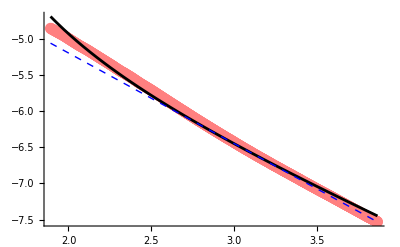
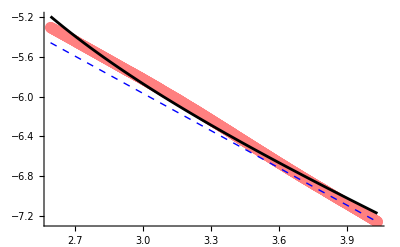
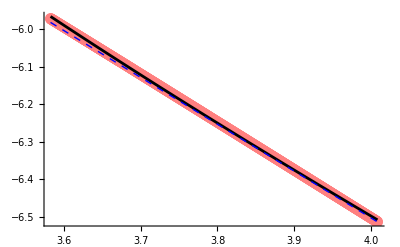
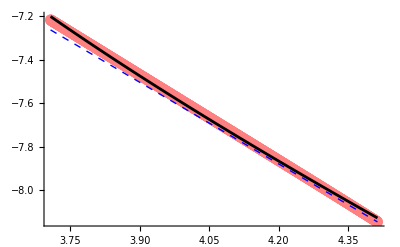
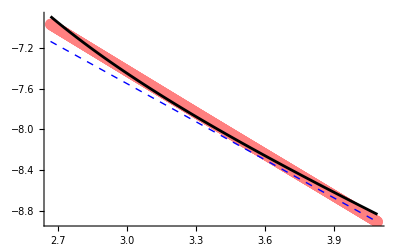
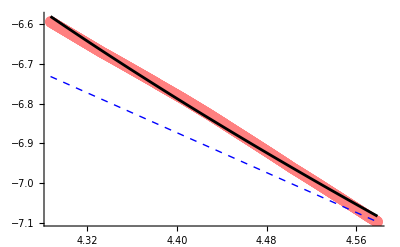
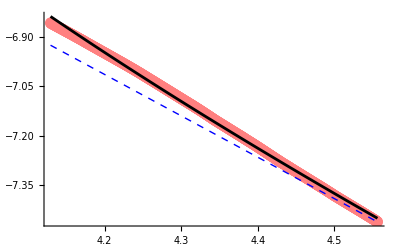
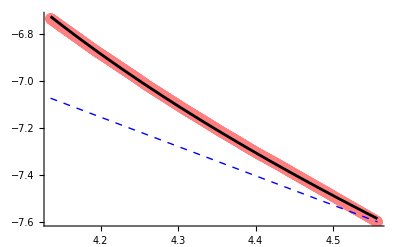
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | Null | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
ArrayReshape[FitETData  /@ Range[16],{4,4}]//TableForm
```

```mathematica
ClearAll[a,b,c];ResidualsETData[n_]:=
Block[{tdata, Edata,  tedata, ltedata, a,b, c,l, e0,e1,l0, l1,n0, res,  N0 , N1 },
 N0 = 1100;
 N1 = 500;
tdata = Flatten[ToExpression /@Import["/Users/am10485/Documents/Wolfram Mathematica/Decaying_turbulence2/case2."<> ToString[n] <>"_t.txt","Table"]];

Edata = Flatten [ToExpression /@Import["/Users/am10485/Documents/Wolfram Mathematica/Decaying_turbulence2/case2."<> ToString[n] <>"_tke.txt","Table"]];
tedata = Select[Transpose[{tdata,Edata}],#[[2]]>0&];
If[Length[tedata] < N0, Return[]];
ltedata = Log[tedata];
e0 = edectab[[1,1]]  ;
e1 = edectab[[-1,1]] ;
l0 = ltedata[[-N0,1]];
l1 = ltedata[[-N1,1]];
(*Print[n,{e0,e1,l0,l1}];*)
nlm =NonlinearModelFit[ltedata[[-N0;;-N1]],
{a + enInterp[Log[Exp[l  ] - c ]],  
 0 < c < Exp[l0]-Exp[e0]
},
{a, c},l];
nlm["FitResiduals"]
];
```

```mathematica
res =Select[Flatten[ResidualsETData /@ Range[16]],NumericQ];
```

```mathematica
Dimensions[res]
```

{9015}

```mathematica
err =StandardDeviation[Flatten[res]]
```

0.0245098

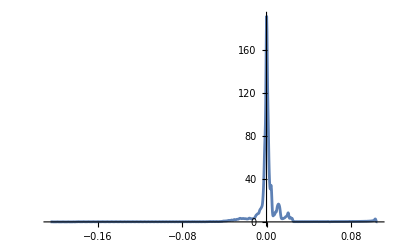

```mathematica
SmoothHistogram[res]
```

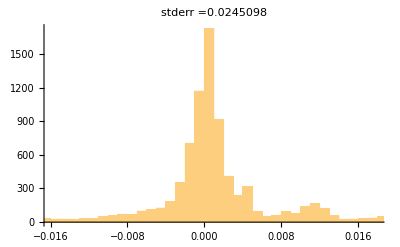

```mathematica
Histogram[res, PlotLabel->"stderr ="<>ToString[err]]
```

```mathematica
(*Animate[ArrayPlot[FitETData[n]],{n,1,16,1},AnimationRunning->False]*)
```

```mathematica
tt = {1,2};
EK = {{e1,e2,e3}, {f1,f2,f3}};
```

```mathematica
hh=EK[[#]] Sqrt[tt[[#]]]& /@ Range[Length[tt]]
```

{{e1,e2,e3},{√2 f1,√2 f2,√2 f3}}

```mathematica
tk = Range[Length[EK[[#]] ]]^2 tt[[#]] & /@ Range[Length[tt]]
```

{{1,4,9},{2,8,18}}

```mathematica
tk[[;;,;;2]]
```

{{1,4},{2,8}}

```mathematica
Transpose[{tk, hh}]
```

{{{1,4,9},{e1,e2,e3}},{{2,8,18},{√2 f1,√2 f2,√2 f3}}}

```mathematica
Range[10] +1
```

{2,3,4,5,6,7,8,9,10,11}

```mathematica
htab={{0.1,0.03690817607609459},{0.10069316688518043,0.03690716863614085},{0.10139113857366795,0.036906154242555625},{0.102093948370768,0.03690513284748546},{0.10280162981264736,0.03690410440276247},{0.1035142166679344,0.03690306885986018},{0.10423174293933042,0.0369020261700067},{0.10495424286523224,0.03690097628403232},{0.10568175092136585,0.036899919152412156},{0.10641430182243161,0.03689885472543311},{0.10715193052376065,0.03689778295290045},{0.10789467222298288,0.03689670378434977},{0.10864256236170655,0.036895617168976734},{0.1093956366272094,0.03689452305561852},{0.1101539309541415,0.03689342139278178},{0.1109174815262401,0.036892312128650386},{0.11168632477805612,0.03689119521104481},{0.11246049739669264,0.03689007058740829},{0.11324003632355571,0.03688893820486436},{0.11402497875611686,0.03688779801016705},{0.1148153621496883,0.036886649949757044},{0.11561122421920988,0.03688549396962191},{0.11641260294104915,0.03688433001548312},{0.11721953655481306,0.03688315803261297},{0.11803206356517298,0.03688197796596577},{0.11885022274370186,0.03688078976010544},{0.11967405313072435,0.03687959335917684},{0.12050359403717975,0.036878388707054975},{0.12133888504649773,0.036877175747068856},{0.12217996601648717,0.03687595442230241},{0.12302687708123816,0.03687472467537014},{0.12387965865303692,0.03687348644849989},{0.1247383514242943,0.0368722396835492},{0.1256029963694875,0.036870984321992616},{0.12647363474711512,0.03686972030482933},{0.12735030810166617,0.036868447572721647},{0.12823305826560213,0.036867166065870184},{0.12912192736135342,0.03686587572413569},{0.13001695780332903,0.03686457648690533},{0.1309181922999407,0.036863268293161854},{0.1318256738556407,0.03686195108149731},{0.13273944577297395,0.03686062479007177},{0.13365955165464424,0.03685928935661844},{0.13458603540559483,0.03685794471843841},{0.1355189412351036,0.036856590812439936},{0.13645831365889247,0.036855227575063085},{0.13740419750125152,0.03685385494235669},{0.1383566378971781,0.036852472849912145},{0.13931568029453031,0.036851081232896314},{0.14028137045619582,0.036849680026036724},{0.14125375446227545,0.03684826916362021},{0.142232878712282,0.036846848579494274},{0.14321878992735435,0.036845418207064176},{0.14421153515248689,0.03684397797929459},{0.14521116175877422,0.03684252782867599},{0.14621771744567183,0.03684106768726775},{0.14723125024327188,0.03683959748667031},{0.14825180851459538,0.03683811715802336},{0.14927944095789963,0.03683662663200757},{0.15031419660900225,0.03683512583883462},{0.15135612484362082,0.03683361470823135},{0.15240527537972914,0.03683209316948133},{0.15346169827992945,0.036830561151390884},{0.15452544395384138,0.03682901858226058},{0.15559656316050746,0.03682746538992117},{0.1566751070108149,0.03682590150174783},{0.15776112696993488,0.03682432684456131},{0.1588546748597779,0.03682274134475112},{0.1599558028614669,0.03682114492816624},{0.16106456351782705,0.03681953752018478},{0.162181009735893,0.03681791904565349},{0.16330519478943345,0.03681628942893622},{0.16443717232149316,0.03681464859386219},{0.1655769963469528,0.036812996463760926},{0.1667247212551063,0.03681133296142394},{0.16788040181225605,0.03680965800915282},{0.16904409316432642,0.036807971528684695},{0.1702158508394951,0.036806273441261916},{0.17139573075084255,0.03680456366756788},{0.17258378919902037,0.03680284212776895},{0.17378008287493757,0.03680110874146561},{0.17498466886246572,0.036799363427744536},{0.17619760464116294,0.03679760610512757},{0.1774189480890166,0.036795836691601566},{0.1786487574852051,0.03679405510458024},{0.1798870915128788,0.03679226126094},{0.18113400926196024,0.03679045507699313},{0.18238957023196378,0.03678863646849324},{0.18365383433483465,0.036786805350607785},{0.18492686189780783,0.036784961637953584},{0.18620871366628677,0.03678310524458543},{0.18749945080674188,0.036781236083953624},{0.18879913490962935,0.03677935406894991},{0.19010782799233,0.03677745911187052},{0.19142559250210858,0.03677555112443343},{0.1927524913190936,0.03677363001776133},{0.19408858775927784,0.036771695702389195},{0.19543394557753946,0.036769748088253756},{0.1967886289706845,0.03676778708467827},{0.19815270258050985,0.036765812600380594},{0.19952623149688797,0.036763824543508315},{0.20090928126087282,0.036761822821530496},{0.20230191786782714,0.03675980734134956},{0.20370420777057185,0.03675777800922363},{0.20511621788255652,0.03675573473078821},{0.20653801558105292,0.036753677411045925},{0.20796966871036957,0.036751605954380644},{0.20941124558508928,0.036749520264511476},{0.21086281499332893,0.036747420244528504},{0.21232444620002197,0.0367453057968844},{0.21379620895022322,0.036743176823356496},{0.2152781734724373,0.03674103322507734},{0.2167704104819695,0.03673887490252548},{0.21827299118430019,0.03673670175549721},{0.21978598727848253,0.03673451368313731},{0.22130947096056378,0.03673231058389768},{0.2228435149270304,0.036730092355572404},{0.22438819237827665,0.0367278588952496},{0.22594357702209777,0.03672561009934587},{0.22750974307720706,0.03672334586358639},{0.22908676527677732,0.03672106608299011},{0.2306747188720069,0.036718770651879375},{0.2322736796357107,0.03671645946387097},{0.23388372386593548,0.036714132411876085},{0.23550492838960096,0.03671178938808804},{0.23713737056616552,0.03670943028398513},{0.23878112829131776,0.036707054990320724},{0.24043628000069336,0.03670466339712211},{0.24210290467361784,0.03670225539367708},{0.24378108183687527,0.036699830868555085},{0.24547089156850307,0.036697389709566666},{0.24717241450161304,0.03669493180379046},{0.24888573182823912,0.036692457037549926},{0.2506109253032114,0.03668996529641239},{0.25234807724805747,0.036687456465189706},{0.25409727055493053,0.036684930427931556},{0.2558585886905646,0.036682387067917384},{0.25763211570025757,0.03667982626764752},{0.2594179362118815,0.03667724790885886},{0.26121613543992067,0.03667465187249548},{0.26302679918953825,0.03667203803871414},{0.26485001386067003,0.03666940628688238},{0.266685866452148,0.0366667564955693},{0.26853444456585074,0.03666408854253686},{0.2703958364108844,0.03666140230475095},{0.2722701308077912,0.03665869765834743},{0.27415741719278824,0.036655974478660903},{0.2760577856220346,0.036653232640192365},{0.2779713267759289,0.036650472016620465},{0.27989813196343627,0.036647692480779676},{0.28183829312644537,0.03664489390467623},{0.2837919028441556,0.036642076159466776},{0.2857590543374947,0.036639239115460076},{0.28773984147356696,0.03663638264210529},{0.2897343587701323,0.03663350660799559},{0.2917427014001167,0.0366306108808551},{0.2937649651961531,0.03662769532753581},{0.2958012466551546,0.03662475981401473},{0.297851642942919,0.03662180420537892},{0.29991625189876514,0.036618828365842},{0.30199517204020165,0.03661583215870755},{0.3040885025676279,0.03661281544638735},{0.30619634336906776,0.03660977809038795},{0.3083187950249355,0.03660671995130645},{0.3104559588128356,0.03660364088881688},{0.3126079367123955,0.036600540761682385},{0.31477483141013163,0.03659741942772987},{0.31695674630434917,0.036594276743857256},{0.31915378551007617,0.0365911125660244},{0.3213660538640318,0.0365879267492421},{0.32359365692962827,0.03658471915896758},{0.32583670100200884,0.036581489622909136},{0.328095293113119,0.03657823801947328},{0.3303695410368148,0.03657496417031816},{0.3326595532940045,0.036571667967286905},{0.3349654391578276,0.03656834922311162},{0.33728730865886886,0.03656500782364514},{0.3396252725904084,0.03656164365669593},{0.3419794425137088,0.03655825640041183},{0.3443499307633385,0.03655484604478984},{0.34673685045253166,0.03655141242923162},{0.34914031547858615,0.036547955362688345},{0.35156044052829816,0.03654447462483425},{0.3539973410834347,0.03654097015183337},{0.35645113342624424,0.03653744172422132},{0.3589219346450052,0.03653388918662618},{0.36140986263961333,0.036530312341508525},{0.36391503612720716,0.036526711118396324},{0.3664375746478333,0.036523085275935674},{0.36897759857015033,0.036519434711736576},{0.37153522909717257,0.03651575920185397},{0.37411058827205335,0.03651205862635325},{0.3767037989839089,0.03650833278747321},{0.37931498497368193,0.0365045815249351},{0.3819442708400466,0.03650080467762598},{0.3845917820453536,0.03649700205785825},{0.38725764492161724,0.036493173517957535},{0.38994198667654345,0.036489318861529986},{0.3926449353995999,0.03648543792083277},{0.39536662006812795,0.03648153053982484},{0.3981071705534973,0.03647759652750898},{0.40086671762730286,0.03647363569340051},{0.403645392967605,0.036469647877694356},{0.40644332916521286,0.03646563290305585},{0.4092606597300108,0.03646159056929062},{0.41209751909733017,0.03645752069972486},{0.4149540426343629,0.03645342312291243},{0.4178303666466218,0.0364492976416661},{0.420726628384444,0.03644514406626318},{0.4236429660495411,0.03644096222176673},{0.4265795188015926,0.03643675191289648},{0.42953642676488724,0.036432512940710544},{0.43251383103500873,0.036428245126451396},{0.4355118736855686,0.036423948277808246},{0.4385306977749857,0.03641962218526483},{0.44157044735331247,0.03641526666110322},{0.4446312674691087,0.03641088152073338},{0.4477133041763625,0.036406466551227507},{0.45081670454146017,0.03640202154716848},{0.4539416166502032,0.036397546325166584},{0.4570881896148751,0.036393040681270986},{0.4602565735813561,0.03638850439694724},{0.46344691973628804,0.036383937276151676},{0.46665938031428866,0.036379339122116466},{0.46989410860521547,0.036374709715629484},{0.4731512589614806,0.036370048846700705},{0.47643098680541573,0.03636535631625765},{0.4797334486366892,0.03636063190726996},{0.4830588020397727,0.03635587540126175},{0.4864072056914617,0.03635108659445898},{0.48977881936844625,0.03634626527052574},{0.493173803954936,0.03634141120272532},{0.4965923214503361,0.036336524181674636},{0.5000345349769786,0.03633160399529401},{0.5035006087879048,0.0363266504103384},{0.5069907082747043,0.03632166320418442},{0.5105049999754062,0.03631664216766796},{0.514043651582426,0.036311587070957704},{0.5176068319505677,0.03630649767720109},{0.5211947111050804,0.03630137376927456},{0.5248074602497725,0.03629621512417759},{0.5284452517751804,0.03629102150048601},{0.5321082592667942,0.036285792667628776},{0.5357966575133416,0.03628052840225684},{0.5395106225151277,0.03627522846452065},{0.5432503314924332,0.0362698926146042},{0.5470159628939716,0.03626452062362949},{0.5508076964054034,0.03625911225125379},{0.5546257129579107,0.036253667250394396},{0.5584701947368308,0.036248185386783434},{0.5623413251903492,0.03624266642064752},{0.5662392890382533,0.03623711009725403},{0.5701642722807475,0.03623151617257047},{0.5741164622073276,0.03622588440889373},{0.5780960474057182,0.036220214549953514},{0.5821032177708715,0.03621450633817248},{0.5861381645140288,0.03620875953140115},{0.5902010801718444,0.036202973877811385},{0.5942921586155727,0.03619714911158029},{0.5984115950603197,0.03619128497831502},{0.6025595860743578,0.036185381226754715},{0.6067363295885055,0.036179437590253355},{0.6109420249055721,0.03617345380367579},{0.6151768727098683,0.03616742961014308},{0.6194410750767815,0.03616136474205908},{0.6237348354824194,0.036155258927082795},{0.628058358813318,0.036149111902190764},{0.6324118513762196,0.03614292339804489},{0.6367955209079159,0.0361366931349818},{0.6412095765851618,0.036130420842420644},{0.6456542290346556,0.036124106251068606},{0.6501296903430909,0.036117749076317596},{0.6546361740672751,0.03611134903570322},{0.6591738952443215,0.03610490585729523},{0.6637430704019089,0.03609841925764921},{0.6683439175686148,0.03609188894400334},{0.6729766562843179,0.03608531463457106},{0.6776415076106752,0.036078696046916804},{0.6823386941416698,0.03607203288491817},{0.6870684400142323,0.03606532485563673},{0.6918309709189366,0.036058571672172454},{0.6966265141107688,0.03605177303731204},{0.7014552984199711,0.03604492865042017},{0.7063175542629619,0.03603803821779242},{0.711213513653329,0.03603110143939979},{0.716143410212902,0.036024118007849555},{0.7211074791828995,0.03601708762273328},{0.7261059574351547,0.03601000998204335},{0.7311390834834174,0.03600288477197944},{0.7362070974947361,0.035995711682401926},{0.7413102413009174,0.03598849040921309},{0.7464487584100664,0.03598122063678114},{0.7516228940182055,0.035973902044311515},{0.7568328950209744,0.03596653432037183},{0.762079010025412,0.03595911714968191},{0.7673614893618189,0.03595165020546259},{0.7726805850957024,0.03594413316530947},{0.778036551039804,0.035936565710421954},{0.7834296427662117,0.035928947511867336},{0.7888601176185543,0.03592127823846854},{0.7943282347242815,0.035913557564315954},{0.7998342550070284,0.03590578515721208},{0.8053784411990667,0.03589796067927755},{0.8109610578538407,0.035890083797678},{0.8165823713585925,0.03588215417655535},{0.8222426499470711,0.03587417147111714},{0.8279421637123342,0.03586613534014499},{0.8336811846196343,0.03585804544473187},{0.8394599865193975,0.035849901435425414},{0.84527884516029,0.035841702960495665},{0.8511380382023765,0.03583344967507176},{0.8570378452303697,0.03582514122818381},{0.8629785477669704,0.035816777259875865},{0.8689604292863019,0.0358083574150247},{0.8749837752274362,0.035799881339531235},{0.8810488730080142,0.03579134866954437},{0.8871560120379609,0.035782759040173},{0.8933054837332954,0.035774112090387326},{0.8994975815300352,0.03576540745265077},{0.9057326008982001,0.03575664475468095},{0.9120108393559099,0.03574782362770558},{0.918332596483581,0.03573894369926861},{0.9246981739382227,0.03573000458995036},{0.9311078754678305,0.03572100592306985},{0.9375620069258803,0.03571194732172275},{0.9440608762859235,0.035702828400049645},{0.9506047936562816,0.03569364877161311},{0.9571940712948446,0.0356844080541812},{0.9638290236239707,0.0356751058584037},{0.9705099672454898,0.035665741788504866},{0.9772372209558109,0.03565631545322332},{0.9840111057611338,0.03564682645992604},{0.9908319448927678,0.03563727440703209},{0.9977000638225535,0.03562765889304073},{1.0046157902783954,0.03561797951891671},{1.0115794542598988,0.03560823587885884},{1.018591388054117,0.03559842756314622},{1.0256519262514077,0.03558855416459148},{1.0327614057613976,0.03557861527203622},{1.0399201658290593,0.03556861046865119},{1.0471285480508998,0.03555853933943214},{1.054386896391259,0.035548401467716685},{1.0616955571987248,0.035538196429499055},{1.0690548792226582,0.03552792380083556},{1.0764652136298347,0.03551758315957567},{1.0839269140212033,0.03550717407637113},{1.0914403364487564,0.035496696117591355},{1.0990058394325208,0.03548614885312437},{1.1066237839776663,0.035475531849588564},{1.1142945335917298,0.035464844665885335},{1.1220184543019633,0.03545408686179288},{1.1297959146727976,0.0354432579980359},{1.1376272858234306,0.03543235762843038},{1.1455129414455356,0.03542138530371363},{1.153453257821092,0.03541034057637237},{1.1614486138403428,0.03539922299455915},{1.1694993910198708,0.03538803210145342},{1.1776059735208073,0.03537676744121385},{1.18576874816716,0.03536542855552629},{1.193988104464273,0.035354014979945156},{1.2022644346174127,0.03534252624998291},{1.2105981335504823,0.03533096190105171},{1.2189895989248665,0.035319321461849386},{1.2274392311584073,0.03530760445824845},{1.2359474334445104,0.03529581041823773},{1.2445146117713852,0.035283938865268094},{1.253141174941416,0.03527198931645813},{1.2618275345906707,0.03525996129003113},{1.2705741052085417,0.03524785430351738},{1.2793813041575248,0.03523566786759909},{1.288249551693134,0.03522340149067834},{1.297179270983956,0.03521105468209848},{1.3061708881318417,0.035198626946430396},{1.3152248321922384,0.03518611778376411},{1.3243415351946648,0.03517352669457125},{1.333521432163324,0.03516085317639456},{1.342764961137864,0.03514809672147074},{1.3520725631942774,0.03513525682161387},{1.36144468246595,0.03512233296727736},{1.3708817661648538,0.035109324642917564},{1.380384264602885,0.03509623133093915},{1.3899526312133534,0.03508305251440482},{1.3995873225726183,0.03506978767126009},{1.409288798421875,0.0350564362744763},{1.4190575216890924,0.0350429977979058},{1.428893958511103,0.03502947171328413},{1.4387985782558457,0.03501585748595571},{1.4487718535447618,0.035002154579735656},{1.4588142602753487,0.034988362458553135},{1.468926277643867,0.034974480581236436},{1.4791083881682077,0.03496050840267835},{1.4893610777109156,0.03494644537776696},{1.4996848355023737,0.03493229095811502},{1.5100801541641486,0.03491804459055563},{1.5205475297324957,0.03490370572112688},{1.5310874616820305,0.034889273793785605},{1.5417004529495597,0.03487474824720648},{1.5523870099580825,0.03486012851830879},{1.5631476426409545,0.03484541404345978},{1.5739828644662197,0.03483060425389878},{1.5848931924611138,0.0348156985770325},{1.595879147236733,0.034800696440591965},{1.6069412530128777,0.034785597269148254},{1.6180800376430662,0.03477040048159014},{1.629296032639723,0.03475510549576137},{1.6405897731995396,0.034739711728683245},{1.6519617982290153,0.034724218592102674},{1.6634126503701692,0.03470862549441369},{1.6749428760264373,0.034692931843650014},{1.6865530253887409,0.03467713704422171},{1.6982436524617441,0.034661240496118934},{1.7100153150902875,0.034645241598274736},{1.721868574986007,0.034629139747138035},{1.733803997754138,0.034612934334417596},{1.7458221529205038,0.034596624750053845},{1.7579236139586927,0.034580210382533234},{1.770108958317421,0.034563690615467976},{1.7823787674480895,0.03454706482938047},{1.7947336268325262,0.03453033240437231},{1.807174126010927,0.034513492716733096},{1.8197008586099834,0.034496545137880454},{1.8323144223712113,0.03447948903835523},{1.8450154191794734,0.03446232378696139},{1.8578044550916983,0.034445048747310775},{1.8706821403658005,0.034427663280270394},{1.8836490894898004,0.03441016674596187},{1.8967059212111463,0.0343925585005744},{1.909853258566238,0.034374837896234564},{1.9230917289101583,0.03435700428387368},{1.9364219639466071,0.034339057011682654},{1.9498445997580456,0.03432099542349965},{1.9633602768360465,0.03430281886131646},{1.9769696401118608,0.03428452666513739},{1.990673338987187,0.03426611817049544},{2.004472027365161,0.03424759271029177},{2.018366363681561,0.034228949616353775},{2.0323570109362215,0.03421018821651072},{2.046444636724674,0.03419130783455873},{2.06062991327,0.0341723077933804},{2.07491351745491,0.034153187413419564},{2.0892961308540396,0.03413394601029967},{2.1037784397664754,0.03411458289746846},{2.118361135248502,0.034095097387229115},{2.1330449131465765,0.03407548878780082},{2.1478304741305343,0.03405575640382133},{2.1627185237270203,0.03403589953871845},{2.177709772353159,0.03401591749303497},{2.192804935350449,0.03399580956332605},{2.2080047330189,0.033975575044340615},{2.2233098906514033,0.033955213228634824},{2.23872113856834,0.03393472340474525},{2.2542392121524295,0.033914104858867394},{2.2698648518838223,0.03389335687567296},{2.2855988033754304,0.03387247873598231},{2.301441817408509,0.03385146971731764},{2.3173946499684788,0.03383032909612705},{2.3334580622810033,0.033809056146009236},{2.3496328208483077,0.03378765013632521},{2.365919697485759,0.033766110334719414},{2.382319469358691,0.03374443600731829},{2.398832919019491,0.033722626416236745},{2.415460834444941,0.03370068082059658},{2.432204009073816,0.03367859847833735},{2.4490632418447458,0.03365637864443344},{2.46603933723434,0.03363402057026},{2.483133105295571,0.03361152350553643},{2.500345361696432,0.03358888669776416},{2.517676927758856,0.03356610939084674},{2.5351286304979084,0.033543190826577134},{2.5527013026612466,0.03352013024502223},{2.5703957827688635,0.03349692688275119},{2.5882129151530915,0.033473579973648165},{2.6061535499988953,0.03345008875038357},{2.6242185433844414,0.03342645244270506},{2.642408757321946,0.03340267027683905},{2.6607250597988092,0.03337874147764761},{2.6791683248190314,0.03335466526821583},{2.69773943244492,0.033330440867942894},{2.7164392688390824,0.03330606749389542},{2.735268726306712,0.03328154436201714},{2.7542287033381663,0.03325687068534611},{2.7733201046518405,0.033232045673848944},{2.792543841237338,0.03320706853614012},{2.8119008303989403,0.03318193847875951},{2.831391995799379,0.03315665470513777},{2.851018267503909,0.03313121641694177},{2.870780582024691,0.03310562281421064},{2.8906798823654754,0.033079873094012474},{2.9107171180666054,0.03305396645130801},{2.9308932452503207,0.03302790207987668},{2.9512092266663856,0.03300167917085175},{2.9716660317380263,0.03297529691265968},{2.992264636608189,0.032948754492706914},{3.0130060241861214,0.032922051096619095},{3.0338911841942706,0.03289518590695477},{3.0549211132155136,0.032868158104682924},{3.0760968147407084,0.032840966869819056},{3.0974192992165803,0.03281361137978417},{3.118889584093937,0.032786090809666095},{3.1405086938762174,0.03275840433366091},{3.1622776601683795,0.03273055112419733},{3.1841975217261247,0.03270253035121554},{3.2062693245054663,0.03267434118342082},{3.2284941217126355,0.0326459827882484},{3.250872973854344,0.03261745433082223},{3.2734069487883826,0.03258875497478876},{3.296097121774578,0.03255988388289323},{3.3189445755261042,0.03253084021581176},{3.3419504002611427,0.032501623132398794},{3.3651156937549076,0.032472231790914484},{3.3884415613920256,0.03244266534814712},{3.4119291162192855,0.03241292295868044},{3.4355794789987466,0.03238300377629795},{3.4593937782612194,0.03235290695414226},{3.483373150360118,0.03232263164334564},{3.507518739525681,0.03229217699362643},{3.53183169791957,0.032261542154396236},{3.556313185689854,0.03223072627378695},{3.580964371026361,0.032199728498251604},{3.605786430216425,0.03216854797374441},{3.6307805477010144,0.03213718384553891},{3.65594791613125,0.03210563525741185},{3.681289736425315,0.03207390135244488},{3.706807217825761,0.032041981273389315},{3.7325015779572066,0.032009874161758295},{3.7583740428844425,0.03197757915821935},{3.784425847170934,0.03194509540345273},{3.8106582339377315,0.031912422037322266},{3.8370724549227884,0.031879558198572966},{3.8636697705406924,0.031846503026039565},{3.890451449942807,0.03181325565848001},{3.9174187710778323,0.03177981523356272},{3.9445730207527854,0.031746180888674015},{3.9719154946944037,0.031712351761669505},{3.999447497610976,0.031678326989896866},{4.027170343254592,0.03164410571011641},{4.055085354483839,0.031609687059576584},{4.083193863326922,0.031575070175692756},{4.111497211045224,0.0315402541954318},{4.139996748197305,0.03150523825610553},{4.1686938347033555,0.03147002149559752},{4.197589839910076,0.03143460305165386},{4.226686142656031,0.03139898206233404},{4.255984131337432,0.03136315766661774},{4.285485203974397,0.03132712900370838},{4.315190768277653,0.03129089521301959},{4.345102241715717,0.031254455435141416},{4.375221051582522,0.031217808811501106},{4.405548635065535,0.03118095448371297},{4.436086439314327,0.03114389159445994},{4.466835921509633,0.03110661928791307},{4.497798548932881,0.031069136708849955},{4.52897579903621,0.031031443002859805},{4.560369159512963,0.030993537317263592},{4.591980128368688,0.030955418800678487},{4.623810213992605,0.03091708660261459},{4.655860935229591,0.03087853987427278},{4.688133821452654,0.030839777768658556},{4.7206304126359075,0.03080079944001956},{4.753352259428055,0.030761604044325982},{4.786300923226385,0.03072219073971831},{4.819477976251275,0.030682558685957338},{4.852885001621213,0.03064270704458036},{4.886523593428334,0.030602634979643564},{4.920395356814508,0.030562341657338846},{4.9545019080479005,0.030521826245660535},{4.988844874600121,0.030481087915253204},{5.02342589522387,0.030440125839574176},{5.058246620031139,0.03039893919419279},{5.093308710571953,0.030357527157214754},{5.128613839913648,0.030315888910008124},{5.164163692720709,0.03027402363670662},{5.199959965335158,0.030231930524032016},{5.236004365857501,0.030189608762083035},{5.272298614228227,0.030147057544341542},{5.308844442309883,0.030104276067237454},{5.345643593969715,0.030061263530665107},{5.382697825162882,0.03001801913833211},{5.420008904016237,0.02997454209733639},{5.457578610912709,0.029930831618420264},{5.495408738576245,0.02988688691654776},{5.5335010921573655,0.029842707210561897},{5.571857489319298,0.029798291723093232},{5.610479760324704,0.029753639681310787},{5.649369748123025,0.029708750316919618},{5.688529308438413,0.029663622865682512},{5.727960309858291,0.029618256567977466},{5.767664633922506,0.029572650669317246},{5.80764417521312,0.029526804419861327},{5.847900841444806,0.02948071707445985},{5.888436553555889,0.02943438789339771},{5.929253245799997,0.02938781614230425},{5.970352865838368,0.02934100109185246},{6.01173737483278,0.029293942018319134},{6.053408747539135,0.029246638203858182},{6.09536897240169,0.02919908893617368},{6.137620051647941,0.02915129350883556},{6.180164001384158,0.029103251221749362},{6.223002851691594,0.029054961380886986},{6.266138646723353,0.029006423298357443},{6.309573444801932,0.028957636293042877},{6.353309318517436,0.028908599690519843},{6.39734835482648,0.02885931282280108},{6.441692655151773,0.028809775028945092},{6.486344335482383,0.02875998565539364},{6.531305526474724,0.028709944055559863},{6.576578373554205,0.02865964959006616},{6.62216503701762,0.02860910162740282},{6.668067692136221,0.028558299543765774},{6.714288529259523,0.02850724272290769},{6.760829753919818,0.028455930556735506},{6.807693586937415,0.02840436244551061},{6.854882264526616,0.028352537797602217},{6.902398038402419,0.028300456029858735},{6.950243175887969,0.02824811656801348},{6.998419960022734,0.028195518846492244},{7.046930689671469,0.02814266230859828},{7.095777679633888,0.028089546407029358},{7.144963260755133,0.028036170603807167},{7.194489780036995,0.027982534370213207},{7.244359600749902,0.027928637187376794},{7.2945751025456875,0.027874478546482097},{7.345138681571149,0.02782005794848313},{7.396052750582378,0.027765374904479553},{7.44731973905989,0.02771042893626321},{7.498942093324558,0.027655219576129007},{7.550922276654339,0.027599746366881027},{7.6032627694018196,0.02754400886245024},{7.655966069112563,0.02748800662801745},{7.709034690644301,0.02743173923985335},{7.762471166286918,0.027375206285738352},{7.816278045883298,0.027318407365330612},{7.870457896950987,0.027261342090029304},{7.925013304804718,0.027204010083216757},{7.9799468726797675,0.027146410980744235},{8.035261221856173,0.02708854443085948},{8.090958991783824,0.027030410094277434},{8.147042840208398,0.02697200764473579},{8.203515443298183,0.026913336769116687},{8.260379495771788,0.026854397167300082},{8.31763771102671,0.026795188552629867},{8.375292821268827,0.026735710652340625},{8.433347577642754,0.02667596320737694},{8.491804750363139,0.026615945972563372},{8.550667128846834,0.02655565871719241},{8.609937521846009,0.026495101225083317},{8.66961875758217,0.026434273294510004},{8.729713683881117,0.02637317473868337},{8.790225168308845,0.02631180538606135},{8.851156098308357,0.02625016508026156},{8.912509381337456,0.026188253680365932},{8.974287945007488,0.026126071061349215},{9.036494737223016,0.026063617114056255},{9.099132726322518,0.02600089174536235},{9.162204901219999,0.02593789487867779},{9.225714271547634,0.025874626454033853},{9.289663867799366,0.02581108642806523},{9.354056741475521,0.025747274774509478},{9.418895965228415,0.025683191484525587},{9.484184633008974,0.025618836566565356},{9.549925860214362,0.025554210046664454},{9.61612278383665,0.02548931196897742},{9.682778562612494,0.025424142395781356},{9.749896377173872,0.025358701407506533},{9.817479430199846,0.02529298910325395},{9.885530946569391,0.025227005601044666},{9.954054173515273,0.025160751037769016},{10.023052380779,0.025094225569541977},{10.092528860766848,0.025027429372096552},{10.16248692870696,0.0249603626407849},{10.232929922807545,0.024893025590797046},{10.303861204416165,0.024825418457617272},{10.37528415818013,0.02475754149709855},{10.447202192208003,0.024689394985543508},{10.519618738232232,0.02462097922019492},{10.592537251772892,0.02455229451946896},{10.665961212302582,0.02448334122289568},{10.739894123412451,0.024414119691494478},{10.814339512979384,0.02434463030822728},{10.88930093333434,0.024274873477968754},{10.964781961431854,0.024204849627639174},{11.040786199020737,0.02413455920672733},{11.117317272815917,0.024064002687465957},{11.19437883467152,0.02399318056481689},{11.271974561755108,0.023922093356869973},{11.350108156723156,0.023850741605191645},{11.42878334789772,0.0237791258748296},{11.508003889444362,0.02370724675456825},{11.587773561551257,0.02363510485734308},{11.668096170609623,0.02356270082030525},{11.748975549395292,0.02349003530496267},{11.830415557251644,0.023417108997634842},{11.912420080273744,0.023343922609618258},{11.994993031493784,0.023270476877189864},{12.0781383510678,0.023196772562019196},{12.161860006463677,0.023122810451522403},{12.246161992650483,0.023048591358813136},{12.331048332289086,0.02297411612291936},{12.416523075924108,0.022899385609273192},{12.502590302177198,0.02282440070980081},{12.58925411794167,0.02274916234294354},{12.676518658578452,0.022673671454085602},{12.764388088113435,0.02259792901583446},{12.852866599436153,0.022521936028006406},{12.941958414499858,0.022445693517905672},{13.03166778452299,0.022369202540693318},{13.12199899019203,0.02229246417942179},{13.212956341865748,0.022215479545198542},{13.304544179780908,0.022138249777590623},{13.396766874259349,0.02206077604472472},{13.489628825916533,0.02198305954332737},{13.583134465871538,0.021905101499133512},{13.677288255958487,0.021826903167132292},{13.772094688939461,0.021748465831499496},{13.867558288718882,0.021669790805872266},{13.963683610559375,0.021590879433770825},{14.060475241299137,0.021511733088587816},{14.157937799570815,0.021432353173638154},{14.25607593602188,0.021352741122592812},{14.354894333536558,0.021272898399651838},{14.454397707459274,0.021192826499478144},{14.554590805819657,0.021112526947487907},{14.655478409559116,0.02103200130015325},{14.757065332758945,0.02095125114496453},{14.859356422870068,0.020870278100596416},{14.962356560944333,0.02078908381727405},{15.066070661867418,0.020707669976795823},{15.170503674593366,0.020626038292576563},{15.275660582380723,0.02054419051003184},{15.381546403030345,0.020462128406660427},{15.488166189124811,0.020379853791868286},{15.595525028269535,0.0202973685073198},{15.703628043335522,0.02021467442744024},{15.812480392703831,0.0201317734590937},{15.9220872705117,0.020048667541522992},{16.032453906900415,0.019965358646945174},{16.143585568264864,0.019881848780989503},{16.25548755750484,0.019798139980849516},{16.368165214278086,0.019714234318423472},{16.48162391525508,0.019630133898043127},{16.595869074375607,0.01954584085749993},{16.710906143107078,0.019461357367810714},{16.82674061070467,0.019376685633597065},{16.943378004473285,0.019291827892931036},{17.060823890031237,0.019206786417642976},{17.17908387157588,0.019121563513105122},{17.298163592151017,0.019036161316128442},{17.41806873391614,0.018950582807249036},{17.538805018417612,0.018864829785791407},{17.660378206861644,0.018778904894960882},{17.78279410038923,0.01869281060936356},{17.906058540352944,0.01860654943765382},{18.03017740859569,0.018520123922633535},{18.155156627731355,0.018433536640686383},{18.281002161427427,0.01834679017155047},{18.40772001468956,0.01825988725292858},{18.535316234148116,0.018172830470435157},{18.6637969083467,0.01808562256776736},{18.793168168032686,0.01799826629157624},{18.923436186449756,0.017910764422547548},{19.054607179632473,0.017823119775216514},{19.186687406702898,0.017735335198019758},{19.31968317016924,0.017647413573297292},{19.45360081622663,0.01755935781712474},{19.5884467350599,0.01747117087930386},{19.72422736114854,0.01738285574337526},{19.860949173573715,0.017294415508279076},{19.998618696327444,0.017205852978959924},{20.137242498623888,0.017117171484970235},{20.276827195212825,0.01702837408693333},{20.417379446695296,0.016939463859815138},{20.55890595984142,0.016850444062598925},{20.701413487910425,0.01676131788665061},{20.844908830972894,0.016672088426382636},{20.989398836235246,0.01658275942833096},{21.134890398366473,0.01649333361447703},{21.281390459827122,0.01640381485025397},{21.428906011200592,0.016314206190344377},{21.57744409152667,0.016224511114212286},{21.72701178863745,0.016134733084350438},{21.87761623949553,0.01604487557503343},{22.02926463053457,0.015954942091913612},{22.181964198002195,0.01586493617183744},{22.335722228305322,0.015774861348497905},{22.49054605835782,0.01568472132242751},{22.646443075930605,0.015594519620356774},{22.803420720004187,0.015504259935373034},{22.96148648112363,0.015413945956365246},{23.120647901755955,0.015323581401857113},{23.280912576650085,0.015233170048680291},{23.44228815319923,0.015142715586860001},{23.60478233180578,0.015052221908797372},{23.768402866248774,0.014961692819526166},{23.933157564053882,0.014871132240265546},{24.099054286865957,0.01478054388314054},{24.266100950824164,0.01468993184279743},{24.434305526939724,0.014599300004147234},{24.60367604147628,0.014508652337836868},{24.774220576332866,0.014417992840650007},{24.945947269429556,0.014327325530942016},{25.11886431509581,0.01423665446998778},{25.292979964461455,0.014145983717638923},{25.46830252585042,0.01405531746870724},{25.64484036517718,0.013964659566798536},{25.822601906345973,0.01387401443545745},{26.001595631652727,0.01378338615056069},{26.18183008218986,0.01369277890343576},{26.36331385825381,0.013602196837493499},{26.546055619755403,0.01351164439829835},{26.73006408663312,0.01342112563200988},{26.91534803926917,0.013330644885897558},{27.10191631890844,0.013240206457260933},{27.289777828080418,0.013149814663029074},{27.47894153102396,0.013059473839194383},{27.669416454115108,0.01296918834021787},{27.861211686297697,0.012878962538474625},{28.054336379517128,0.012788800823675438},{28.248799749157065,0.012698707602232543},{28.444611074479152,0.012608687307303126},{28.641779699065797,0.012518744344980863},{28.84031503126605,0.012428883200043959},{29.040226544644497,0.012339108328894302},{29.241523778433347,0.012249424212139159},{29.444216337987605,0.012159835347288851},{29.64831389524342,0.012070346227957465},{29.853826189179586,0.011980961281694328},{30.0607630262823,0.011891685337570582},{30.269134281013052,0.011802522628615156},{30.478949896279826,0.01171347780399101},{30.690219883911567,0.01162455541983527},{30.902954325135898,0.011535760040193698},{31.11716337106017,0.011447096236251975},{31.33285724315585,0.011358568628247852},{31.550046233746258,0.01127018169998568},{31.7687407064977,0.011181940081831395},{31.988951096913976,0.011093848408858242},{32.21068791283434,0.011005911247872507},{32.43396173493492,0.010918133196653395},{32.65878321723358,0.010830518854590025},{32.88516308759829,0.010743072821873804},{33.113112148259106,0.010655799698647096},{33.34264127632349,0.010568704084142328},{33.57376142429546,0.010481790575849158},{33.80648362059815,0.010395063768654967},{34.040818970100084,0.010308528244133086},{34.27677865464503,0.010222188663978117},{34.514373933585624,0.010136049444852416},{34.753616144320574,0.01005011530787937},{34.994516702835725,0.009964390776412195},{35.23708710424871,0.00987888041107855},{35.48133892335754,0.00979358876363919},{35.727283815192884,0.009708520376051048},{35.97493351557423,0.009623679779549251},{36.22429984166986,0.009539071493719188},{36.475394692560776,0.009454700025541723},{36.72823004980847,0.009370569868450808},{36.98281797802662,0.009286685485430992},{37.23917062545685,0.009203051387870798},{37.49730022454835,0.009119671974953588},{37.757219092541604,0.009036551692351544},{38.01893963205612,0.008953694951433555},{38.28247433168226,0.008871106144241591},{38.54783576657718,0.008788789596806863},{38.815036599064825,0.008706749796771527},{39.08408957924021,0.008624990935213336},{39.35500754557775,0.008543517362838805},{39.627803425543945,0.008462333360422047},{39.902490236214206,0.008381443183531616},{40.179081084893994,0.008300851077207386},{40.45758916974427,0.008220561196600914},{40.73802778041127,0.008140577762750015},{41.020410298660686,0.008060904904817433},{41.30475019901614,0.007981546737485804},{41.591061049402214,0.007902507344300584},{41.87935651179184,0.007823790776673212},{42.16965034285823,0.007745401053954837},{42.461956394631294,0.007667342157155144},{42.756288615158624,0.007589618038572663},{43.052661049171064,0.007512232610189914},{43.35108783875289,0.007435189748015452},{43.651583224016605,0.007358493290054828},{43.954161543782455,0.007282147035330831},{44.25883723626266,0.007206154751606078},{44.565624839750335,0.007130520131009627},{44.87453899331322,0.00705524687647905},{45.18559443749224,0.006980338613577361},{45.49880601500487,0.00690579892833007},{45.81418867145335,0.006831631367297873},{46.131757456037946,0.006757839432741123},{46.451527522274944,0.006684426575937745},{46.773514128719825,0.00661139619912842},{47.097732639695295,0.006538751670739757},{47.42419852602447,0.006466496285045415},{47.7529273657691,0.006394633288752509},{48.083934844972866,0.006323165935950172},{48.41723675840994,0.006252097340162681},{48.75284901033864,0.006181430599346065},{49.09078761526032,0.006111168813873512},{49.43106869868355,0.0060413149114978285},{49.77370849789361,0.0059718718823108885},{50.11872336272724,0.005902842572549477},{50.46612975635284,0.005834229839199618},{50.81594425605606,0.005766036412541104},{51.16818355403078,0.005698265065374172},{51.52286445817566,0.005630918382956441},{51.88000389289612,0.005563998990833698},{52.23961889991199,0.005497509416471873},{52.60172663907063,0.0054314521424930476},{52.9663443891658,0.00536582954173244},{53.33348954876212,0.005300644013686955},{53.70317963702529,0.005235897762893174},{54.0754322945581,0.005171593100892873},{54.450265284242136,0.005107732118056468},{54.82769649208539,0.005044316907507298},{55.20774392807576,0.0049813494974967325},{55.590425727040376,0.004918831878667875},{55.97576014951103,0.004856765898321145},{56.363765582595455,0.0047951533887264424},{56.75446054085472,0.00473399611424839},{57.147863667186726,0.004673295776902656},{57.54399373371571,0.004613053964162529},{57.94286964268812,0.004553272216877311},{58.3445104273745,0.004493952081836011},{58.74893525297769,0.0044350948958204895},{59.15616341754742,0.004376702042413541},{59.56621435290107,0.004318774758943379},{59.97910762555096,0.004261314275728325},{60.39486293763801,0.004204321688683699},{60.813500127871805,0.004147798082717575},{61.23503917247737,0.00409174441104541},{61.65950018614824,0.0040361616178706435},{62.08690342300638,0.003981050507414082},{62.51726927756861,0.003926411875489358},{62.950618285719784,0.003872246398736866},{63.386971125692725,0.003818554713971411},{63.8263486190549,0.003765337373249957},{64.26877173170199,0.0037125948262510702},{64.71426157485834,0.0036603275040165153},{65.16283940608425,0.003608535728678103},{65.61452663029051,0.0035572197585922367},{66.06934480075958,0.003506379779354353},{66.52731562017412,0.003456015903862686},{66.98846094165262,0.0034061281838677787},{67.45280276979217,0.0033567165527745636},{67.92036326171844,0.003307780940418964},{68.39116472814291,0.0032593211586041345},{68.86522963442759,0.0032113369586126155},{69.34258060165689,0.0031638280199697433},{69.82324040771712,0.003116793950692654},{70.30723198838332,0.0030702342875656547},{70.79457843841378,0.003024148496447258},{71.28530301265194,0.0029785359726014556},{71.77942912713615,0.0029333960410518373},{72.27698036021701,0.002888727956966729},{72.77798045368239,0.002844530906072235},{73.2824533138904,0.0028008040050863333},{73.79042301291007,0.0027575463021801473},{74.30191378967012,0.002714756777469409},{74.81695005111543,0.0026724343435287007},{75.33555637337172,0.002630577845928715},{75.85775750291836,0.002589186063802775},{76.38357835776905,0.0025482577104384316},{76.91304402866095,0.002507791433890291},{77.44617978025185,0.00246778581761944},{77.98301105232586,0.0024282393811589816},{78.52356346100717,0.002389150580800115},{79.06786279998249,0.0023505178103020493},{79.61593504173186,0.002312339401628335},{80.1678063387679,0.0022746136257035705},{80.72350302488381,0.0022373386931905928},{81.28305161640992,0.0022005127552932216},{81.84647881347898,0.0021641339045807297},{82.41381150130022,0.002128200175829742},{82.98507675144225,0.002092709546888485},{83.5603018231248,0.002057659939564057},{84.1395141645195,0.0020230492205264607},{84.72274141405964,0.0019888752022306426},{85.31001140175893,0.0019551356438605116},{85.90135215053957,0.0019218282522905378},{86.49679187756932,0.001888950683062351},{87.09635899560806,0.0018565005413803718},{87.70008211436347,0.0018244753831250665},{88.30799004185627,0.001792872715879523},{88.92011178579484,0.0017616899999719697},{89.53647655495938,0.0017309246495350182},{90.15711376059568,0.0017005740335769668},{90.78205301781857,0.0016706354770656402},{91.41132414702503,0.0016411062620276392},{92.04495717531712,0.0016119836286591373},{92.68298233793492,0.0015832647764456912},{93.3254300796991,0.0015549468652946584},{93.97233105646379,0.001527027016679336},{94.6237161365793,0.0014995023147898572},{95.27961640236519,0.0014723698076925796},{95.94006315159332,0.0014456265085000858},{96.60508789898134,0.0014192693965474356},{97.2747223776965,0.001393295418573244},{97.9489985408699,0.001367701489908521},{98.62794856312105,0.0013424844956712062},{99.31160484209339,0.0013176412919631935},{100.,0.0012931687070718146}};
```

```mathematica
htab1 ={{100.1,0.0012896582112289},{100.33065405102548,0.0012816036636367528},{100.5618395834821,0.001273589734632992},{100.79355782202863,0.0012656163048390453},{101.02580999414575,0.0012576832545751347},{101.25859733014256,0.001249790463865405},{101.49192106316312,0.0012419378124426071},{101.72578242919289,0.0012341251797542804},{101.96018266706534,0.0012263524449664547},{102.19512301846852,0.0012186194869685369},{102.43060472795163,0.0012109261843791836},{102.66662904293158,0.001203272415550737},{102.90319721369966,0.0011956580585746805},{103.14031049342809,0.0011880829912855777},{103.3779701381767,0.001180547091266578},{103.61617740689961,0.0011730502358552294},{103.85493356145184,0.001165592302147232},{104.09423986659603,0.001158173167001802},{104.33409759000912,0.0011507927070464647},{104.5745080022891,0.0011434507986823994},{104.81547237696168,0.001136147318089655},{105.05699199048715,0.0011288821412308186},{105.29906812226695,0.001121655143856888},{105.54170205465068,0.001114466201512392},{105.7848950729427,0.0011073151895399042},{106.02864846540905,0.0011002019830851472},{106.27296352328422,0.0010931264571011979},{106.51784154077804,0.0010860884863545367},{106.76328381508246,0.001079087945429734},{107.0092916463785,0.0010721247087334227},{107.2558663378431,0.001065198650500009},{107.50300919565602,0.0010583096447962072},{107.75072152900675,0.0010514575655265327},{107.99900465010154,0.0010446422864375765},{108.24785987417013,0.0010378636811223536},{108.49728851947302,0.0010311216230264428},{108.74729190730815,0.0010244159854521334},{108.99787136201819,0.001017746641563283},{109.24902821099727,0.0010111134643899955},{109.50076378469822,0.0010045163268333933},{109.75307941663954,0.0009979551016713695},{110.0059764434125,0.0009914296615622842},{110.2594562046881,0.0009849398790498349},{110.51352004322436,0.0009784856265683771},{110.76816930487328,0.0009720667764474162},{111.02340533858805,0.0009656832009167106},{111.27922949643012,0.0009593347721101368},{111.53564313357644,0.0009530213620709051},{111.79264760832665,0.0009467428427569498},{112.05024428211011,0.0009404990860446525},{112.3084345194934,0.0009342899637339014},{112.56721968818724,0.0009281153475525538},{112.82660115905395,0.0009219751091615011},{113.08658030611461,0.0009158691201595524},{113.34715850655644,0.0009097972520869295},{113.60833714073992,0.0009037593764308091},{113.87011759220628,0.0008977553646298957},{114.13250124768473,0.0008917850880788613},{114.39548949709982,0.0008858484181329708},{114.65908373357885,0.0008799452261120145},{114.92328535345919,0.0008740753833059431},{115.18809575629571,0.000868238760979021},{115.45351634486816,0.0008624352303737881},{115.71954852518866,0.000856664662716065},{115.98619370650911,0.0008509269292192076},{116.25345330132863,0.0008452219010891413},{116.52132872540112,0.0008395494495282},{116.78982139774266,0.0008339094457392479},{117.05893274063911,0.0008283017609310542},{117.32866417965357,0.0008227262663221672},{117.59901714363407,0.0008171828331453188},{117.86999306472094,0.0008116713326516137},{118.14159337835457,0.0008061916361148453},{118.41381952328288,0.0008007436148366425},{118.68667294156907,0.0007953271401497897},{118.96015507859916,0.0007899420834226602},{119.23426738308967,0.0007845883160638535},{119.50901130709535,0.0007792657095262299},{119.78438830601677,0.0007739741353115062},{120.0603998386081,0.0007687134649735658},{120.33704736698489,0.0007634835701232202},{120.61433235663168,0.000758284322432774},{120.89225627640982,0.0007531155936394517},{121.17082059856533,0.0007479772555498266},{121.4500267987366,0.0007428691800436032},{121.72987635596222,0.0007377912390782345},{122.01037075268886,0.0007327433046929721},{122.29151147477907,0.0007277252490120877},{122.57330001151922,0.0007227369442495746},{122.85573785562731,0.000717778262713085},{123.13882650326096,0.00071284907680785},{123.42256745402521,0.0007079492590405724},{123.70696221098066,0.000703078682022864},{123.99201228065118,0.0006982372184760341},{124.27771917303218,0.0006934247412346346},{124.5640844015983,0.0006886411232498829},{124.85110948331169,0.000683886237593882},{125.13879593862991,0.0006791599574631922},{125.42714529151402,0.0006744621561831747},{125.71615906943661,0.0006697927072111347},{126.00583880338998,0.00066515148413985},{126.29618602789414,0.0006605383607020651},{126.58720228100506,0.0006559532107736687},{126.87888910432274,0.000651395908377518},{127.17124804299932,0.0006468663276867378},{127.46428064574744,0.0006423643430284523},{127.75798846484828,0.0006378898288879778},{128.0523730561598,0.0006334426599115465},{128.34743597912518,0.0006290227109100445},{128.64317879678075,0.0006246298568626701},{128.9396030757645,0.000620263972920383},{129.23671038632438,0.0006159249344095696},{129.53450230232656,0.0006116126168347447},{129.83298040126365,0.0006073268958824431},{130.1321462642633,0.0006030676474248831},{130.43200147609642,0.0005988347475227617},{130.7325476251856,0.0005946280724288047},{131.03378630361348,0.0005904474985907773},{131.33571910713135,0.0005862929026552086},{131.63834763516738,0.0005821641614706312},{131.94167349083526,0.0005780611520900719},{132.2456982809426,0.0005739837517748719},{132.5504236159995,0.000569931837997686},{132.85585111022704,0.0005659052884456934},{133.16198238156582,0.0005619039810235706},{133.46881905168468,0.0005579277938561563},{133.77636274598896,0.0005539766052923091},{134.0846150936295,0.0005500502939075245},{134.39357772751103,0.0005461487385067084},{134.70325228430085,0.0005422718181273301},{135.01364040443755,0.0005384194120422188},{135.3247437321397,0.0005345913997629532},{135.63656391541446,0.0005307876610421499},{135.9491026060665,0.0005270080758762358},{136.26236145970657,0.0005232525245088159},{136.57634213576034,0.0005195208874331173},{136.8910462974772,0.0005158130453948692},{137.20647561193906,0.0005121288793947305},{137.5226317500692,0.0005084682706911205},{137.83951638664104,0.0005048311008033878},{138.15713120028713,0.0005012172515137637},{138.47547787350797,0.0004976266048701571},{138.79455809268097,0.0004940590431888396},{139.1143735480693,0.0004905144490569951},{139.4349259338309,0.00048699270533545644},{139.7562169480275,0.0004834936951605208},{140.07824829263348,0.0004800173019469334},{140.4010216735451,0.0004765634093904537},{140.72453880058927,0.0004731319014699122},{141.04880138753285,0.0004697226624497465},{141.37381115209155,0.00046633557688205093},{141.69956981593913,0.00046297052960941475},{142.02607910471653,0.0004596274057670764},{142.35334074804092,0.0004563060907847012},{142.68135647951493,0.00045300647038907745},{143.01012803673584,0.00044972843060619414},{143.33965716130476,0.00044647185776354947},{143.66994559883582,0.00044323663849210647},{144.00099509896557,0.00044002265972814124},{144.33280741536194,0.0004368298087159614},{144.66538430573397,0.0004336579730096471},{144.99872753184061,0.000430507040474922},{145.33283885950058,0.0004273768992912792},{145.66772005860128,0.0004242674379538425},{146.00337290310844,0.0004211785452757485},{146.33979917107536,0.0004181101103895217},{146.67700064465242,0.0004150620227489375},{147.0149791100966,0.00041203417213131276},{147.35373635778063,0.0004090264486390221},{147.69327418220286,0.000406038742701475},{148.0335943819965,0.00040307094507650675},{148.3746987599393,0.0004001229468523311},{148.71658912296294,0.000397194639449595},{149.0592672821628,0.00039428591462248704},{149.4027350528074,0.00039139666446060006},{149.74699425434804,0.0003885267813905159},{150.09204671042855,0.00038567615817751617},{150.43789424889476,0.0003828446879272354},{150.7845387018044,0.0003800322640866625},{151.1319819054366,0.00037723878044607453},{151.48022570030173,0.00037446413114059103},{151.8292719311512,0.0003717082106513661},{152.1791224469871,0.00036897091380710576},{152.52977910107202,0.0003662521357852187},{152.88124375093903,0.0003635517721136054},{153.2335182584013,0.00036086971867187916},{153.58660448956203,0.00035820587169226595},{153.94050431482444,0.0003555601277612834},{154.2952196089016,0.0003529323838208365},{154.6507522508263,0.000350322537169621},{155.0071041239611,0.00034773048546410585},{155.36427711600828,0.0003451561267194826},{155.72227311901983,0.00034259935931136464},{156.08109402940744,0.000340060081976563},{156.44074174795267,0.00033753819381413663},{156.80121817981677,0.000335033594286455},{157.1625252345511,0.0003325461832201955},{157.52466482610706,0.00033007586080771324},{157.88763887284605,0.0003276225276075251},{158.25144929755007,0.0003251860845453144},{158.61609802743158,0.00032276643291512784},{158.9815869941437,0.0003203634743800861},{159.34791813379067,0.0003179771109733725},{159.7150933869379,0.00031560724509875247},{160.08311469862235,0.0003132537795315907},{160.45198401836277,0.00031091661741990264},{160.8217033001701,0.00030859566228466764},{161.19227450255778,0.00030629081802073353},{161.56369958855208,0.00030400198889748097},{161.9359805257026,0.00030172907955962813},{162.3091192860926,0.0002994719950279674},{162.68311784634952,0.000297230640699522},{163.0579781876554,0.0002950049223485616},{163.4337022957574,0.00029279474612718166},{163.81029216097832,0.0002906000185657105},{164.18774977822707,0.00028842064657329843},{164.56607714700937,0.00028625653743818833},{164.94527627143825,0.0002841075988286328},{165.32534916024474,0.00028197373879316573},{165.70629782678836,0.0002798548657607848},{166.08812428906793,0.0002777508885416294},{166.47083056973227,0.000275661716327252},{166.8544186960908,0.000273587258691168},{167.23889070012436,0.0002715274255889498},{167.62424861849593,0.0002694821273584222},{168.01049449256146,0.0002674512747203683},{168.39763036838073,0.00026543477877854127},{168.78565829672797,0.0002634325510198912},{169.17458033310308,0.00026144450331475874},{169.56439853774214,0.0002594705479170654},{169.95511497562856,0.0002575105974647984},{170.34673171650402,0.0002555645649797369},{170.7392508348793,0.0002536323638676479},{171.13267441004538,0.00025171390791860237},{171.52700452608437,0.0002498091113069077},{171.9222432718807,0.00024791788859130774},{172.31839274113193,0.0002460401547146893},{172.71545503236015,0.0002441758250043379},{173.11343224892286,0.00024232481517210585},{173.5123264990242,0.00024048704131403594},{173.91213989572609,0.00023866241991047895},{174.31287455695949,0.00023685086782592254},{174.71453260553554,0.0002350523023090916},{175.11711616915682,0.00023326664099283223},{175.52062738042875,0.0002314938018936317},{175.92506837687063,0.00022973370341179732},{176.33044130092722,0.00022798626433125974},{176.7367482999799,0.00022625140381931857},{177.14399152635815,0.00022452904142642455},{177.55217313735096,0.0002228190970857849},{177.9612952952182,0.00022112149111347645},{178.3713601672021,0.00021943614420801585},{178.78236992553872,0.00021776297744987764},{179.19432674746943,0.00021610191230140633},{179.60723281525256,0.00021445287060638626},{180.0210903161748,0.0002128157745898914},{180.43590144256294,0.00021119054685768795},{180.85166839179536,0.00020957711039577834},{181.26839336631375,0.0002079753885703556},{181.68607857363466,0.0002063853051271497},{182.10472622636138,0.00020480678419103918},{182.52433854219555,0.0002032397502655149},{182.94491774394885,0.00020168412823225686},{183.36646605955494,0.00020013984335089745},{183.78898572208107,0.0001986068212581459},{184.2124789697401,0.0001970849879673779},{184.6369480459021,0.00019557426986820613},{185.06239519910665,0.00019407459372587296},{185.48882268307423,0.00019258588668076223},{185.9162327567186,0.00019110807624754338},{186.34462768415852,0.00018964109031479072},{186.77400973472984,0.0001881848571444834},{187.2043811829975,0.00018673930537111745},{187.63574430876753,0.00018530436400117657},{188.0681013970992,0.00018387996241238489},{188.50145473831714,0.0001824660303532013},{188.93580662802336,0.00018106249794212157},{189.37115936710953,0.00017966929566667263},{189.80751526176905,0.00017828635438298996},{190.24487662350944,0.00017691360531503354},{190.68324576916436,0.00017555098005382101},{191.12262502090613,0.0001741984105566474},{191.56301670625774,0.0001728558291461597},{192.00442315810554,0.00017152316850990945},{192.44684671471123,0.00017020036169936706},{192.89028971972454,0.00016888734212900516},{193.33475452219542,0.00016758404357560455},{193.7802434765867,0.00016629040017734627},{194.22675894278632,0.0001650063464331438},{194.67430328612005,0.000163731817201541},{195.12287887736392,0.0001624667476998208},{195.57248809275674,0.00016121107350337016},{196.0231333140128,0.00015996473054461028},{196.47481692833435,0.0001587276551121254},{196.9275413284244,0.00015749978384964623},{197.38130891249924,0.00015628105375517848},{197.83612208430128,0.00015507140218025243},{198.29198325311165,0.00015387076682866265},{198.7488948337631,0.00015267908575559687},{199.20685924665273,0.00015149629736673544},{199.66587891775467,0.00015032234041723012},{200.12595627863325,0.00014915715401078608},{200.58709376645567,0.0001480006775983947},{201.04929382400474,0.0001468528509775434},{201.51255889969227,0.0001457136142912483},{201.9768914475717,0.00014458290802682697},{202.44229392735113,0.00014346067301495771},{202.9087688044064,0.0001423468504285146},{203.37631854979438,0.00014124138178170639},{203.84494564026554,0.00014014420892894446},{204.31465255827752,0.0001390552740635534},{204.78544179200816,0.00013797451971691346},{205.2573158353685,0.00013690188875731027},{205.73027718801634,0.00013583732438885435},{206.20432835536914,0.00013478077015030698},{206.67947184861745,0.00013373216991386882},{207.15571018473827,0.0001326914678843185},{207.63304588650826,0.0001316586085977286},{208.11148148251712,0.00013063353692024886},{208.59101950718107,0.00012961619804705249},{209.07166250075616,0.00012860653750113065},{209.55341300935194,0.00012760450113229353},{210.0362735849446,0.00012661003511578965},{210.52024678539087,0.0001256230859511276},{211.00533517444117,0.00012464360046110498},{211.49154132175366,0.000123671525790466},{211.9788678029074,0.00012270680940477531},{212.46731719941627,0.00012174939908909578},{212.95689209874263,0.0001207992429468719},{213.44759509431077,0.00011985628939886797},{213.93942878552113,0.00011892048718169137},{214.4323957777635,0.00011799178534668231},{214.92649868243123,0.00011707013325870412},{215.42174011693507,0.0001161554805949338},{215.91812270471664,0.0001152477773436621},{216.41564907526268,0.00011434697380284673},{216.91432186411907,0.00011345302057906375},{217.41414371290435,0.00011256586858628732},{217.91511726932416,0.00011168546904451013},{218.41724518718493,0.00011081177347854642},{218.92053012640827,0.00010994473371669099},{219.4249747530447,0.00010908430188962612},{219.93058173928804,0.0001082304304291007},{220.43735376348945,0.00010738307206648693},{220.9452935101716,0.00010654217983170213},{221.45440367004315,0.0001057077070518729},{221.96468694001248,0.00010487960735009934},{222.47614602320252,0.00010405783464410289},{222.98878362896468,0.00010324234314486167},{223.50260247289344,0.00010243308735556778},{224.01760527684064,0.00010163002207017762},{224.53379476892994,0.00010083310237209903},{225.05117368357108,0.00010004228363293832},{225.56974476147477,0.00009925752151118023},{226.0895107496668,0.00009847877195103536},{226.6104744015028,0.0000977059911809333},{227.13263847668279,0.00009693913571225684},{227.65600574126577,0.00009617816233817264},{228.18057896768445,0.00009542302813222814},{228.70636093475977,0.0000946736904470916},{229.23335442771582,0.00009393010691313049},{229.7615622381945,0.00009319223543719656},{230.29098716427032,0.00009246003420142067},{230.82163201046512,0.00009173346166170048},{231.3534995877631,0.00009101247654647389},{231.88659271362573,0.00009029703785541437},{232.42091421200632,0.00008958710485814697},{232.95646691336543,0.00008888263709296257},{233.4932536546857,0.00008818359436531897},{234.03127727948666,0.00008748993674671069},{234.57054063784014,0.00008680162457335758},{235.11104658638519,0.00008611861844480125},{235.65279798834317,0.00008544087922264109},{236.19579771353307,0.0000847683680291318},{236.74004863838644,0.00008410104624605028},{237.28555364596306,0.00008343887551329872},{237.83231562596575,0.00008278181772748156},{238.380337474756,0.00008212983504073763},{238.92962209536915,0.00008148288985937728},{239.4801723975299,0.00008084094484263461},{240.03199129766753,0.00008020396290126608},{240.58508171893152,0.0000795719071962066},{241.13944659120693,0.00007894474113744716},{241.69508885113012,0.0000783224283826053},{242.25201144210394,0.00007770493283561001},{242.81021731431372,0.00007709221864541776},{243.36970942474258,0.00007648425020470474},{243.93049073718728,0.00007588099214868498},{244.49256422227387,0.00007528240935363744},{245.0559328574735,0.00007468846693564288},{245.62059962711794,0.00007409913024939853},{246.18656752241571,0.00007351436488684042},{246.75383954146773,0.0000729341366759067},{247.32241868928327,0.00007235841167912898},{247.89230797779584,0.00007178715619244627},{248.46351042587915,0.0000712203367439958},{249.03602905936313,0.00007065792009266018},{249.6098669110499,0.00007009987322687555},{250.1850270207299,0.00006954616336332645},{250.76151243519797,0.00006899675794573069},{251.3393262082695,0.0000684516246435623},{251.91847140079656,0.00006791073135063742},{252.49895108068412,0.00006737404618400377},{253.0807683229064,0.0000668415374826583},{253.663926209523,0.00006631317380623966},{254.24842782969546,0.00006578892393378231},{254.8342762797033,0.00006526875686240047},{255.42147466296066,0.00006475264180618095},{256.01002609003274,0.00006424054819485974},{256.59993367865223,0.00006373244567248674},{257.1912005537357,0.00006322830409629549},{257.78382984740034,0.00006272809353541749},{258.3778246989805,0.00006223178426970556},{258.9731882550442,0.00006173934678841253},{259.56992366941,0.00006125075178893191},{260.1680341031635,0.00006076597017573147},{260.7675227246744,0.00006028497305900944},{261.3683927096127,0.000059807731753489534},{261.9706472409663,0.00005933421777719115},{262.5742895090572,0.00005886440285022878},{263.17932271155877,0.000058398258893701005},{263.7857500535125,0.00005793575802832065},{264.3935747473451,0.00005747687257327011},{265.0028000128855,0.00005702157504505946},{265.6134290773817,0.000056569838156290276},{266.2254651755183,0.00005612163481449811},{266.8389115494332,0.000055676938120860095},{267.453771448735,0.00005523572136911162},{268.0700481305202,0.000054797958044411026},{268.68774485939036,0.00005436362182204173},{269.30686490746956,0.000053932686566301795},{269.92741155442144,0.00005350512632931673},{270.549388087467,0.00005308091534993158},{271.1727978014015,0.00005266002805254694},{271.7976439986124,0.00005224243904584319},{272.42392998909656,0.00005182812312176577},{273.05165909047787,0.00005141705525435812},{273.68083462802485,0.00005100921059859179},{274.31145993466816,0.000050604564489237016},{274.9435383510183,0.000050203092439670475},{275.5770732253834,0.00004980477014088969},{276.2120679137869,0.000049409573460303624},{276.8485257799851,0.00004901747844056375},{277.48645019548553,0.00004862846129852772},{278.1258445395642,0.000048242498424114},{278.76671219928386,0.00004785956637926162},{279.40905656951185,0.0000474796418967329},{280.0528810529382,0.000047102701879017394},{280.6981890600932,0.00004672872339735416},{281.34498400936627,0.00004635768369055598},{281.99326932702326,0.00004598956016394056},{282.64304844722506,0.00004562433038823063},{283.2943248120458,0.00004526197209850333},{283.94710187149064,0.00004490246319319586},{284.6013830835147,0.00004454578173291037},{285.2571719140409,0.000044191905939400196},{285.91447183697846,0.00004384081419456132},{286.57328633424135,0.00004349248503934949},{287.23361889576665,0.00004314689717276783},{287.89547301953314,0.000042804029450726355},{288.5588522115797,0.00004246386088510244},{289.22375998602394,0.000042126370642737215},{289.8901998650809,0.00004179153804431013},{290.55817537908166,0.0000414593425633756},{291.22769006649185,0.00004112976382531028},{291.89874747393077,0.00004080278160637324},{292.5713511561898,0.00004047837583267326},{293.2455046762515,0.000040156526579077434},{293.92121160530843,0.00003983721406832692},{294.59847552278177,0.000039520418670015006},{295.2773000163409,0.00003920612089959796},{295.95768868192175,0.000038894301417396045},{296.63964512374616,0.00003858494102758215},{297.32317295434115,0.0000382780206773222},{298.0082757945577,0.00003797352145573518},{298.6949572735901,0.000037671424592897244},{299.3832210289951,0.00003737171145893904},{300.0730707067114,0.00003707436356306996},{300.7645099610786,0.00003677936255268692},{301.45754245485705,0.00003648669021234632},{302.1521718592467,0.000036196328462828914},{302.848401853907,0.00003590825936030344},{303.5462361269759,0.00003562246509531871},{304.2456783750901,0.00003533892799190488},{304.94673230340396,0.00003505763050662093},{305.6494016256094,0.000034778555227671976},{306.35369006395575,0.00003450168487406191},{307.05960134926903,0.000034227002294572114},{307.7671392209722,0.00003395449046691745},{308.4763074271045,0.00003368413249686842},{309.1871097243417,0.000033415911617356274},{309.89954987801593,0.00003314981118760437},{310.6136316621353,0.000032885814692164765},{311.3293588594041,0.000032623905740133816},{312.0467352612432,0.000032364068064290644},{312.7657646678095,0.00003210628552016691},{313.48645088801646,0.0000318505420852223},{314.20879773955426,0.00003159682185796333},{314.9328090489097,0.0000313451090571571},{315.6584886513869,0.00003109538802095899},{316.3858403911275,0.0000308476432060011},{317.11486812113066,0.00003060185918664916},{317.84557570327405,0.000030358020654144715},{318.5779670083339,0.000030116112415783196},{319.3120459160057,0.000029876119394075206},{320.04781631492443,0.000029638026625898545},{320.78528210268564,0.00002940181926179123},{321.52444718586594,0.000029167482565070857},{322.2653154800433,0.00002893500191101975},{323.00789090981834,0.000028704362786121353},{323.7521774088349,0.000028475550787251746},{324.49817891980064,0.00002824855162094791},{325.2458993945084,0.00002802335110253675},{325.9953427938568,0.000027799935155378044},{326.7465130878713,0.00002757828981015427},{327.4994142557252,0.00002735840120404684},{328.25405028576074,0.00002714025557999109},{329.0104251755104,0.00002692383928587957},{329.7685429317178,0.000026709138773845217},{330.52840757035887,0.000026496140599551023},{331.2900231166637,0.00002628483142135392},{332.0533936051371,0.000026075197999605376},{332.81852307958053,0.00002586722719592638},{333.5854155931133,0.000025660905972474275},{334.354075208194,0.000025456221391227252},{335.1245059966421,0.00002525316061318731},{335.8967120396595,0.000025051710897742547},{336.67069742785225,0.00002485185960195448},{337.446466261252,0.000024653594179797374},{338.2240226493379,0.00002445690218148441},{339.00337071105827,0.00002426177125273502},{339.7845145748525,0.000024068189134146872},{340.5674583786729,0.000023876143660467223},{341.3522062700066,0.000023685622759855695},{342.1387624058974,0.000023496614453275224},{342.927130952968,0.000023309106853785003},{343.7173160874421,0.00002312308816588436},{344.50932199516615,0.00002293854668481054},{345.30315287163205,0.00002275547079586069},{346.09881292199884,0.000022573848973810085},{346.8963063611155,0.00002239366978219522},{347.6956374135428,0.000022214921872654627},{348.496810313576,0.000022037593984299584},{349.2998293052673,0.000021861674943064488},{350.1046986424479,0.000021687153661110004},{350.91142258875095,0.00002151401913611412},{351.72000541763424,0.000021342260450659134},{352.5304514124024,0.000021171866771656346},{353.34276486622974,0.00002100282734967636},{354.15695008218324,0.00002083513151835137},{354.9730113732451,0.000020668768693720065},{355.79095306233563,0.000020503728373656053},{356.6107794823361,0.000020340000137291947},{357.4324949761119,0.000020177573644337696},{358.2561038965355,0.000020016438634525565},{359.08161060650895,0.000019856584927010596},{359.90901947898794,0.000019698002419794613},{360.73833489700445,0.000019540681089138866},{361.5695612536896,0.000019384610988921714},{362.4027029522978,0.000019229782250132066},{363.2377644062292,0.000019076185080284755},{364.0747500390538,0.000018923809762820567},{364.9136642845344,0.00001877264665655247},{365.75451158665004,0.000018622686195081244},{366.5972963996202,0.000018473918886293092},{367.4420231879276,0.00001832633531176936},{368.28869642634214,0.000018179926126197778},{369.1373205999449,0.000018034682056881152},{369.98790020415146,0.000017890593903171267},{370.840439744736,0.000017747652535945215},{371.6949437378549,0.000017605848897038586},{372.55141671007095,0.000017465173998701477},{373.4098631983773,0.000017325618923139022},{374.27028775022126,0.000017187174821928496},{375.1326949235287,0.0000170498329155008},{375.9970892867277,0.00001691358449262838},{376.8634754187735,0.000016778420909909826},{377.731857909172,0.000016644333591298264},{378.6022413580045,0.000016511314027522547},{379.47463037595213,0.00001637935377561106},{380.34902958431996,0.000016248444458421294},{381.22544361506164,0.00001611857776411397},{382.103877110804,0.000015989745445674012},{382.9843347248715,0.000015861939320381506},{383.866821121311,0.000015735151269367056},{384.7513409749165,0.000015609373237144105},{385.6378989712537,0.000015484597231071468},{386.52649980668514,0.000015360815320908544},{387.4171481883946,0.000015238019638337487},{388.3098488344126,0.000015116202376509458},{389.2046064736409,0.000014995355789574709},{390.101425845878,0.000014875472192169934},{391.00031170184377,0.000014756543959019777},{391.9012688032051,0.000014638563524469566},{392.8043019226006,0.000014521523382010725},{393.7094158436664,0.00001440541608384103},{394.6166153610613,0.000014290234240395044},{395.5259052804919,0.000014175970519957433},{396.43729041873837,0.000014062617648183585},{397.35077560367995,0.000013950168407639134},{398.2663656743204,0.000013838615637409157},{399.1840654808138,0.000013727952232646445},{400.1038798844899,0.000013618171144166648},{401.02581375788026,0.000013509265377985628},{401.9498719847439,0.000013401227994899535},{402.8760594600932,0.000013294052110116708},{403.8043810902197,0.000013187730892796985},{404.73484179272026,0.000013082257565644773},{405.66744649652304,0.00001297762540449698},{406.60220014191356,0.000012873827737924073},{407.53910768056096,0.00001277085794685364},{408.4781740755444,0.000012668709464112822},{409.41940430137885,0.000012567375774053113},{410.36280334404177,0.00001246685041217884},{411.30837620099965,0.00001236712696473243},{412.25612788123425,0.000012268199068318108},{413.2060634052691,0.000012170060409478938},{414.1581878051964,0.00001207270472435228},{415.1125061247034,0.000011976125798299918},{416.0690234190991,0.00001188031746548117},{417.02774475534125,0.000011785273608508363},{417.988675212063,0.00001169098815806169},{418.95181987959984,0.000011597455092543115},{419.91718386001685,0.000011504668437698274},{420.884772267135,0.000011412622266213604},{421.8545902265592,0.00001132131069740761},{422.82664287570464,0.000011230727896856089},{423.8009353638245,0.00001114086807602807},{424.77747285203685,0.000011051725491930466},{425.7562605133525,0.00001096329444674411},{426.7373035327019,0.000010875569287521378},{427.7206071069628,0.000010788544405805515},{428.7061764449879,0.000010702214237272435},{429.6940167676321,0.00001061657326142008},{430.6841333077807,0.000010531616001216857},{431.67653131037656,0.000010447337022784212},{432.6712160324482,0.000010363730935030329},{433.66819274313764,0.000010280792389321436},{434.6674667237282,0.00001019851607919626},{435.66904326767246,0.000010116896740000531},{436.67292768062043,0.00001003592914857215},{437.6791252804476,9.955608122913046*^-6},{438.6876413972831,9.875928521879834*^-6},{439.69848137353785,9.796885244891858*^-6},{440.7116505639331,9.71847323156408*^-6},{441.72715433552855,9.64068746142232*^-6},{442.7449980677509,9.563522953604254*^-6},{443.7651871524223,9.486974766541422*^-6},{444.7877269937889,9.411037997662154*^-6},{445.81262300854956,9.335707783055988*^-6},{446.83988062588446,9.260979297212647*^-6},{447.86950528748395,9.186847752725314*^-6},{448.90150244757734,9.11330839996208*^-6},{449.9358775729616,9.04035652679239*^-6},{450.97263614303074,8.967987458286499*^-6},{452.0117836498043,8.89619655644854*^-6},{453.0533255979571,8.824979219916908*^-6},{454.0972675048476,8.75433088364987*^-6},{455.1436149005479,8.684247018685687*^-6},{456.19237332787264,8.614723131849027*^-6},{457.24354834240825,8.545754765467765*^-6},{458.29714551254256,8.477337497094218*^-6},{459.3531704194945,8.409466939218862*^-6},{460.41162865734333,8.342138739040703*^-6},{461.47252583305817,8.275348578163344*^-6},{462.53586756652845,8.209092172319235*^-6},{463.6016594905925,8.143365271125585*^-6},{464.66990725106854,8.078163657808869*^-6},{465.74061650678374,8.013483148963492*^-6},{466.813792929605,7.949319594256072*^-6},{467.8894422044681,7.885668876177427*^-6},{468.96757002940836,7.822526909816018*^-6},{470.04818211559086,7.759889642574035*^-6},{471.13128418734044,7.697753053923904*^-6},{472.21688198217214,7.636113155146422*^-6},{473.30498125082164,7.574965989097205*^-6},{474.39558775727573,7.514307629974842*^-6},{475.48870727880256,7.4541341830354716*^-6},{476.5843456059828,7.394441784371128*^-6},{477.6825085427396,7.33522660067623*^-6},{478.78320190637,7.276484829001999*^-6},{479.88643152757544,7.2182126965241254*^-6},{480.9922032504926,7.1604064602790645*^-6},{482.1005229327244,7.1030624069645935*^-6},{483.21139644537124,7.04617685270772*^-6},{484.32482967306163,6.989746142807566*^-6},{485.44082851398406,6.933766651524947*^-6},{486.5593988799173,6.878234781843604*^-6},{487.6805466962627,6.823146965270052*^-6},{488.8042779020751,6.768499661594596*^-6},{489.9305984500942,6.714289358647631*^-6},{491.05951430677607,6.660512572116194*^-6},{492.1910314523253,6.607165845310806*^-6},{493.32515588072584,6.554245748952639*^-6},{494.46189359977353,6.501748880948357*^-6},{495.60125063110746,6.4496718661725614*^-6},{496.743233010242,6.3980113562898594*^-6},{497.88784678659886,6.346764029515359*^-6},{499.03509802353886,6.295926590403912*^-6},{500.1849927983944,6.2454957696562066*^-6},{501.3375372025014,6.1954683239088915*^-6},{502.49273734123165,6.14584103554624*^-6},{503.65059933402534,6.096610712468412*^-6},{504.81112931442306,6.0477741879003134*^-6},{505.97433343009874,5.999328320216481*^-6},{507.1402178428917,5.951269992719203*^-6},{508.30878872883994,5.903596113451398*^-6},{509.48005227821227,5.856303614989732*^-6},{510.65401469554143,5.809389454266429*^-6},{511.83068219965696,5.7628506123903385*^-6},{513.0100610237179,5.716684094420613*^-6},{514.1921574152459,5.67088692920039*^-6},{515.3769776361587,5.625456169170102*^-6},{516.5645279628026,5.58038889018264*^-6},{517.7548146859864,5.535682191320248*^-6},{518.9478441110142,5.491333194687322*^-6},{520.143622557719,5.447339045261987*^-6},{521.3421563604963,5.403696910710035*^-6},{522.5434518683378,5.360403981190451*^-6},{523.7475154448641,5.317457469188279*^-6},{524.9543534683595,5.2748546093305445*^-6},{526.1639723318056,5.232592658234103*^-6},{527.3763784429144,5.1906688943165076*^-6},{528.5915782241634,5.1490806176091055*^-6},{529.8095781128283,5.107825149614195*^-6},{531.0303845610184,5.066899833124996*^-6},{532.2540040357101,5.026302032061268*^-6},{533.4804430187809,4.986029131293192*^-6},{534.7097080070441,4.946078536472483*^-6},{535.9418055122837,4.906447673897973*^-6},{537.1767420612881,4.867133990326228*^-6},{538.4145241958846,4.828134952810782*^-6},{539.655158472975,4.789448048550323*^-6},{540.8986514645694,4.751070784726429*^-6},{542.1450097578215,4.7130006883614344*^-6},{543.3942399550632,4.675235306132177*^-6},{544.6463486738401,4.6377722042280385*^-6},{545.9013425469457,4.600608968211978*^-6},{547.1592282224572,4.563743202850402*^-6},{548.4200123637709,4.527172531968854*^-6},{549.6837016496366,4.490894598287676*^-6},{550.9503027741939,4.454907063290228*^-6},{552.2198224470069,4.419207607080305*^-6},{553.4922673931007,4.3837939282085135*^-6},{554.767644352996,4.348663743543162*^-6},{556.0459600827451,4.3138147881252575*^-6},{557.3272213539683,4.2792448150278565*^-6},{558.6114349538892,4.244951595212249*^-6},{559.8986076853705,4.210932917367288*^-6},{561.1887463669506,4.17718658779622*^-6},{562.4818578328793,4.143710430272263*^-6},{563.777948933154,4.1105022858878316*^-6},{565.0770265335565,4.077560012925934*^-6},{566.3790975156884,4.044881486715532*^-6},{567.6841687770087,4.012464599518666*^-6},{568.9922472308695,3.980307260380038*^-6},{570.3033398065527,3.948407394983542*^-6},{571.6174534493075,3.916762945543241*^-6},{572.934595120386,3.885371870661476*^-6},{574.2547717970812,3.8542321452065205*^-6},{575.5779904727626,3.823341760170294*^-6},{576.904258156915,3.7926987225420523*^-6},{578.2335818751743,3.7623010552041736*^-6},{579.5659686693651,3.7321467967840338*^-6},{580.901425597538,3.7022340015324562*^-6},{582.2399597340071,3.672560739202519*^-6},{583.5815781693874,3.6431250949283956*^-6},{584.9262880106324,3.6139251691138073*^-6},{586.2740963810716,3.5849590772871387*^-6},{587.6250104204483,3.556224949992879*^-6},{588.9790372849576,3.5277209326840594*^-6},{590.3361841472839,3.499445185591136*^-6},{591.6964581966397,3.4713958836106768*^-6},{593.0598666388025,3.443571216176567*^-6},{594.426416696154,3.4159693871606898*^-6},{595.7961156077178,3.388588614762772*^-6},{597.168970629198,3.361427131373953*^-6},{598.5449890330178,3.3344831834801306*^-6},{599.9241781083572,3.3077550315465403*^-6},{601.3065451611927,3.281240949913228*^-6},{602.6920975143354,3.2549392266814763*^-6},{604.0808425074696,3.228848163588483*^-6},{605.4727874971924,3.2029660759239918*^-6},{606.8679398570517,3.177291292414671*^-6},{608.2663069775865,3.151822155111819*^-6},{609.6678962663647,3.1265570192882884*^-6},{611.0727151480233,3.101494253328515*^-6},{612.4807710643075,3.0766322386431997*^-6},{613.8920714741098,3.0519693695500805*^-6},{615.3066238535098,3.0275040531654687*^-6},{616.7244356958139,3.003234709318415*^-6},{618.1455145115946,2.9791597704427384*^-6},{619.5698678287308,2.955277681482623*^-6},{620.9975031924474,2.9315868997813583*^-6},{622.4284281653552,2.908085894984593*^-6},{623.8626503274907,2.8847731489613814*^-6},{625.3001772763573,2.8616471556880494*^-6},{626.7410166269642,2.83870642115578*^-6},{628.1851760118678,2.8159494632757325*^-6},{629.6326630812115,2.7933748117863854*^-6},{631.0834855027665,2.7709810081693375*^-6},{632.5376509619723,2.748766605533243*^-6},{633.9951671619776,2.726730168534294*^-6},{635.456041823681,2.704870273290528*^-6},{636.9202826857714,2.6831855072825567*^-6},{638.3878975047703,2.6616744692676894*^-6},{639.8588940550712,2.6403357691776995*^-6},{641.3332801289823,2.619168028046958*^-6},{642.8110635367667,2.598169877923892*^-6},{644.2922521066845,2.577339961767661*^-6},{645.7768536850336,2.5566769333725968*^-6},{647.264876136192,2.5361794572789575*^-6},{648.7563273426589,2.5158462086945797*^-6},{650.2512152050963,2.495675873404872*^-6},{651.7495476423721,2.4756671476768964*^-6},{653.2513325916004,2.455818738195748*^-6},{654.7565780081844,2.4361293619752114*^-6},{656.2652918658586,2.4165977462713486*^-6},{657.7774821567306,2.3972226285027077*^-6},{659.293156891324,2.3780027561647612*^-6},{660.8123240986205,2.358936886766902*^-6},{662.3349918261022,2.340023787737714*^-6},{663.8611681397948,2.321262236342472*^-6},{665.39086112431,2.3026510196173374*^-6},{666.9240788828881,2.284188934284919*^-6},{668.4608295374414,2.2658747866846796*^-6},{670.0011212285971,2.2477073926826952*^-6},{671.5449621157398,2.2296855776005964*^-6},{673.0923603770561,2.2118081761538743*^-6},{674.6433242095765,2.194074032361668*^-6},{676.1978618292193,2.176481999477237*^-6},{677.7559814708346,2.15903093991175*^-6},{679.3176913882473,2.1417197251666318*^-6},{680.8829998543013,2.1245472357666695*^-6},{682.4519151609024,2.1075123611705153*^-6},{684.0244456190641,2.090613999710171*^-6},{685.6005995589493,2.073851058524413*^-6},{687.180385329916,2.057222453483445*^-6},{688.7638113005615,2.040727109121917*^-6},{690.3508858587658,2.0243639585594847*^-6},{691.9416174117364,2.0081319434469334*^-6},{693.5360143860536,1.992030013897748*^-6},{695.1340852277142,1.976057128407404*^-6},{696.7358384021766,1.9602122537966376*^-6},{698.3412823944054,1.9444943651407984*^-6},{699.950425708917,1.928902445712406*^-6},{701.5632768698239,1.9134354869097434*^-6},{703.1798444208804,1.8980924881826332*^-6},{704.8001369255273,1.882872456985814*^-6},{706.4241629669378,1.8677744087073924*^-6},{708.051931148063,1.8527973666054029*^-6},{709.6834500916766,1.8379403617431028*^-6},{711.3187284404219,1.8232024329247983*^-6},{712.9577748568564,1.8085826266483197*^-6},{714.6005980234983,1.7940799970298635*^-6},{716.2472066428726,1.7796936057425068*^-6},{717.8976094375566,1.7654225219637006*^-6},{719.551815150227,1.7512658223120643*^-6},{721.209832543705,1.7372225907934954*^-6},{722.8716704010039,1.7232919187304907*^-6},{724.5373375253752,1.7094729047084622*^-6},{726.2068427403548,1.6957646545284535*^-6},{727.8801948898102,1.682166281137187*^-6},{729.5574028379879,1.668676904573952*^-6},{731.2384754695585,1.6552956519110583*^-6},{732.923421689666,1.6420216572027022*^-6},{734.6122504239736,1.6288540614342987*^-6},{736.3049706187113,1.615792012451103*^-6},{738.0015912407235,1.6028346649143254*^-6},{739.7021212775161,1.5899811802478996*^-6},{741.4065697373045,1.5772307265821551*^-6},{743.114945649061,1.5645824787017606*^-6},{744.827258062563,1.5520356179827885*^-6},{746.5435160484407,1.5395893323545844*^-6},{748.2637286982248,1.5272428162442746*^-6},{749.9879051243954,1.5149952705165591*^-6},{751.7160544604302,1.5028459024287955*^-6},{753.4481858608517,1.4907939255767874*^-6},{755.1843085012775,1.4788385598523262*^-6},{756.9244315784674,1.4669790313860054*^-6},{758.668564310373,1.4552145724913344*^-6},{760.416715936186,1.443544421628503*^-6},{762.1688957163877,1.4319678233496635*^-6},{763.9251129327974,1.4204840282502392*^-6},{765.6853768886223,1.409092292918403*^-6},{767.4496969085059,1.397791879885869*^-6},{769.2180823385781,1.386582057592657*^-6},{770.9905425465049,1.3754621003277469*^-6},{772.7670869215368,1.3644312881824842*^-6},{774.54772487456,1.3534889070101324*^-6},{776.3324658381455,1.3426342483768848*^-6},{778.1213192665988,1.3318666095221818*^-6},{779.9142946360109,1.3211852933012958*^-6},{781.7114014443075,1.3105896081465939*^-6},{783.5126492113001,1.3000788680302275*^-6},{785.3180474787357,1.289652392410232*^-6},{787.1276058103481,1.2793095061906717*^-6},{788.9413337919082,1.2690495396735486*^-6},{790.7592410312744,1.2588718285225253*^-6},{792.5813371584444,1.248775713722063*^-6},{794.4076318256053,1.238760541522885*^-6},{796.2381347071852,1.228825663408495*^-6},{798.0728554999044,1.2189704360536487*^-6},{799.911803922827,1.209194221282372*^-6},{801.7549897174116,1.1994963860266031*^-6},{803.6024226475636,1.1898763022779105*^-6},{805.4541124996873,1.1803333470589553*^-6},{807.3100690827362,1.1708669023805678*^-6},{809.1703022282667,1.1614763551951629*^-6},{811.0348217904893,1.152161097362604*^-6},{812.9036376463207,1.1429205256076806*^-6},{814.7767596954365,1.1337540414892525*^-6},{816.6541978603234,1.1246610513547036*^-6},{818.5359620863319,1.1156409662969966*^-6},{820.4220623417293,1.106693202128058*^-6},{822.3125086177514,1.0978171793350732*^-6},{824.2073109286567,1.0890123230452396*^-6},{826.1064793117788,1.0802780629843735*^-6},{828.0100238275797,1.071613833440697*^-6},{829.9179545597032,1.063019073238142*^-6},{831.8302816150277,1.0544932256892552*^-6},{833.747015123721,1.0460357385610146*^-6},{835.6681652392925,1.0376460640418852*^-6},{837.5937421386479,1.0293236587060328*^-6},{839.5237560221434,1.0210679834820785*^-6},{841.4582171136384,1.012878503608298*^-6},{843.397135660551,1.0047546886037618*^-6},{845.3405219339116,9.966960122393006*^-7},{847.288386228418,9.887019524964014*^-7},{849.2407388624882,9.807719915363622*^-7},{851.1975901783177,9.729056156628661*^-7},{853.1589505419319,9.65102315294945*^-7},{855.1248303432421,9.573615849356776*^-7},{857.0952399961008,9.496829231290418*^-7},{859.0701899383564,9.42065832435567*^-7},{861.0496906319081,9.345098193992081*^-7},{863.0337525627623,9.270143945164015*^-7},{865.0223862410874,9.195790722035901*^-7},{867.0156022012693,9.122033707592067*^-7},{869.013411001969,9.048868123439302*^-7},{871.0158232261758,8.9762892294564*^-7},{873.0228494812651,8.904292323452607*^-7},{875.034500399054,8.832872740892069*^-7},{877.0507866358583,8.762025854570328*^-7},{879.0717188725482,8.691747074389779*^-7},{881.0973078146052,8.622031846990574*^-7},{883.1275641921786,8.552875655433834*^-7},{885.1624987601427,8.484274018989902*^-7},{887.2021222981537,8.416222492808485*^-7},{889.2464456107058,8.348716667648323*^-7},{891.2954795271909,8.281752169551195*^-7},{893.3492349019526,8.215324659569782*^-7},{895.4077226143469,8.149429833566162*^-7},{897.4709535687977,8.084063421843187*^-7},{899.5389386948552,8.019221188885145*^-7},{901.6116889472543,7.954898933102303*^-7},{903.6892153059719,7.891092486556868*^-7},{905.7715287762852,7.827797714732047*^-7},{907.8586403888308,7.765010516168814*^-7},{909.9505611996618,7.70272682226181*^-7},{912.0473022903075,7.640942597028395*^-7},{914.1488747678314,7.579653836794919*^-7},{916.2552897648903,7.518856569964195*^-7},{918.3665584397935,7.458546856712131*^-7},{920.4826919765616,7.398720788802817*^-7},{922.6037015849857,7.339374489331656*^-7},{924.729598500687,7.280504112399389*^-7},{926.8603939851762,7.222105842925201*^-7},{928.9960993259132,7.164175896387636*^-7},{931.1367258363667,7.106710518599586*^-7},{933.2822848560749,7.049705985445178*^-7},{935.432787750704,6.993158602592889*^-7},{937.5882459121104,6.937064705346283*^-7},{939.7486707583994,6.881420658373655*^-7},{941.9140737339862,6.82622285544533*^-7},{944.0844663096574,6.771467719220574*^-7},{946.2598599826301,6.71715170099744*^-7},{948.4402662766144,6.663271280549981*^-7},{950.625696741873,6.609822965834596*^-7},{952.8161629552841,6.556803292748434*^-7},{955.0116765204011,6.504208824972647*^-7},{957.2122490675148,6.452036153710724*^-7},{959.4178922537152,6.400281897494595*^-7},{961.6286177629527,6.348942701915851*^-7},{963.8444373061002,6.298015239429403*^-7},{966.0653626210159,6.247496209199237*^-7},{968.2914054726039,6.19738233680654*^-7},{970.5225776528779,6.147670374061803*^-7},{972.758890981023,6.098357098793706*^-7},{975.000357303459,6.049439314655372*^-7},{977.2469884939021,6.000913850938965*^-7},{979.4987964534286,5.952777562293575*^-7},{981.7557931105373,5.905027328575441*^-7},{984.0179904212137,5.857660054665346*^-7},{986.2854003689921,5.810672670233925*^-7},{988.5580349650202,5.764062129557332*^-7},{990.835906248122,5.717825411283191*^-7},{993.1190262848618,5.671959518294582*^-7},{995.407407169608,5.626461477511428*^-7},{997.7010610245976,5.58132833963512*^-7},{999.9999999999999,5.536557179011461*^-7}};
```

```mathematica
htab01 = Join[htab, htab1];
```

```mathematica
Dimensions[htab01]
```

{2002,2}

```mathematica
lhdata = Log[htab01];
```

```mathematica
lhinterp=Interpolation@lhdata;
```

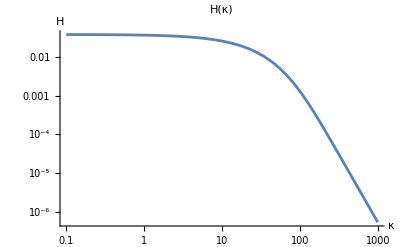

```mathematica
LogLogPlot[Exp[lhinterp[Log[k]]],{k,0.1,1000}, PlotLabel->"H(κ)", AxesLabel->{κ, H}]
```

```mathematica
(Range[0,127]-63.5)^2
```

{4032.25,3906.25,3782.25,3660.25,3540.25,3422.25,3306.25,3192.25,3080.25,2970.25,2862.25,2756.25,2652.25,2550.25,2450.25,2352.25,2256.25,2162.25,2070.25,1980.25,1892.25,1806.25,1722.25,1640.25,1560.25,1482.25,1406.25,1332.25,1260.25,1190.25,1122.25,1056.25,992.25,930.25,870.25,812.25,756.25,702.25,650.25,600.25,552.25,506.25,462.25,420.25,380.25,342.25,306.25,272.25,240.25,210.25,182.25,156.25,132.25,110.25,90.25,72.25,56.25,42.25,30.25,20.25,12.25,6.25,2.25,0.25,0.25,2.25,6.25,12.25,20.25,30.25,42.25,56.25,72.25,90.25,110.25,132.25,156.25,182.25,210.25,240.25,272.25,306.25,342.25,380.25,420.25,462.25,506.25,552.25,600.25,650.25,702.25,756.25,812.25,870.25,930.25,992.25,1056.25,1122.25,1190.25,1260.25,1332.25,1406.25,1482.25,1560.25,1640.25,1722.25,1806.25,1892.25,1980.25,2070.25,2162.25,2256.25,2352.25,2450.25,2550.25,2652.25,2756.25,2862.25,2970.25,3080.25,3192.25,3306.25,3422.25,3540.25,3660.25,3782.25,3906.25,4032.25}

```mathematica
test =TensorProduct[  Range[5],Range[0,4-1]^2]
```

{{0,1,4,9},{0,2,8,18},{0,3,12,27},{0,4,16,36},{0,5,20,45}}

```mathematica
Length[test]
```

5

```mathematica
Plus @@((#[[1]]^2 + #[[2]]^2) & /@ test)
```

55

```mathematica
Length[lhdata]
```

2002

```mathematica
parab =LinearModelFit[Log[htab01],{x, x^2, x^3, x^4},x]
```

FittedModel[-3.37908+«19» x+«1»-«20» x^3+0.00292005 x^4]

```mathematica
parab[x]
```

-3.37908+0.183361 x+0.0107871 x^2-0.0599965 x^3+0.00292005 x^4

```mathematica
parab["EstimatedVariance"]
```

0.0234747

```mathematica
parab["AdjustedRSquared"]
```

0.998298

```mathematica
P1=ListPlot[Log[htab01],PlotStyle->Red];
P2 = Plot[parab[x],{x,Log[htab01[[1,1]]],Log[htab01[[-1,1]]]}];
```

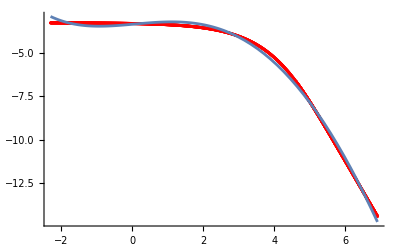

```mathematica
Show[{P1,P2}, PlotRange->All]
```

```mathematica
ClearAl[hh,tk];
```

```mathematica
FitSpectrum[n_]:=
Block[{tdata, Sdata,  tsdata, ltsdata, ltsdata3,hh,ff, tk,tt, sdatas,RR,
a,b,c,r2, l0, e0,var,err,rule,abc,L,L2,L3, T, N0=1100, N1 = 500},
ff[x_] := parab[x];
(*ff[x_] := x;*)
tdata = 1 +Flatten[ToExpression /@Import["/Users/am10485/Documents/Wolfram Mathematica/Decaying_turbulence2/case2."<> ToString[n] <>"_t.txt","Table"]];
T = Length[tdata];
sdatas = ToExpression /@Import["/Users/am10485/Documents/Wolfram Mathematica/Decaying_turbulence2/case2."<> ToString[n] <>"_ek.txt","Table"];
L = Length[sdatas[[1]]];
L2 =4; (*L-128;*)
L3 = L/4;
(*Print[sdatas[[;;10]]];*)
trange =  Range[T][[-N0;;-N1]];
hh=Flatten[sdatas[[#]][[L2;;L3]] Sqrt[tdata[[#]]]& /@trange];
(*Print[sdatas];*)
RR =(Range[L2-1,L3-1]/L)^2;
tk =  TensorProduct[tdata[[-N0;;-N1]],RR]//Flatten;
(*Print["tk: ",Dimensions[tk]];*)
(*Print[tk];*)
(*Return[{tk, hh}];*)
tt =TensorProduct[tdata[[-N0;;-N1]],Table[1,{l,L2,L3}]]//Flatten;
(*Print["tt: ",Dimensions[tt]];
Print[Dimensions/@{sdatas, tt, tk, hh}];*)
tsdata = Select[Transpose[{tt, tk, hh}], (#[[2]]>0 &&#[[3]]>0)&];
If[Length[tsdata] < N0, 
Print[n," failed"];
Return[]];
ltsdata3 = Log[tsdata];
ltsdata =Sort[Join[{#[[2]],#[[3]]}& /@ ltsdata3]];
l0 =ltsdata[[1,1]];
e0 = lhdata[[1,1]];
nlm =NonlinearModelFit[ltsdata,
{a +   ff[ b +  x]},
{a, b},x,Method->"NMinimize"];
var = nlm["EstimatedVariance"];
err = Sqrt[var];
r2 = nlm["AdjustedRSquared"];
(*Print[nlm[x]];*)
P2 = Plot[nlm[x],{x,ltsdata[[1,1]] ,ltsdata[[-1,1]]}, 
PlotStyle->{Green}(*, PlotLegends->{"Theory"}*)];
P1 = ListPlot[ltsdata,
PlotStyle->{Red, PointSize[0.005]}(*, PlotLegends->{"DNS"}*)];
Show[{P1, P2}
,PlotLabel->ToString[n]<>": R2=" <>  ToString[r2] <>" , std=" <> ToString[err]
(*,AxesLabel->{"Log(t k^2)","Log(E(k,t) Sqrt[t])"},PlotRange->All*)]
]//Quiet;
```

```mathematica
8163*512
```

4179456

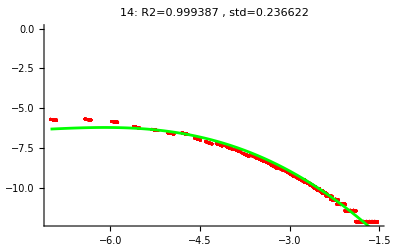

```mathematica
FitSpectrum[14]
```

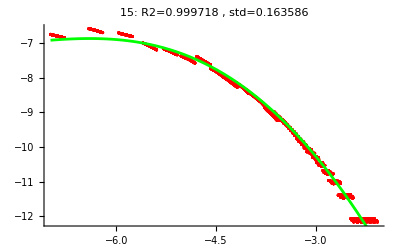
{-Graphics-,-Graphics-}

```mathematica
GraphicsArray[FitSpectrum /@ {14,15}]
```